## Connectivity profiles scale

```mathematica
Subscript[σ, AB]={{7,5,4,0,7,15},{5,6,6,0,5,15},{8,6,0,6,0,15},{5,6,6,0,0,15}};
```

```mathematica
colorgrads={"CandyColors","LightTerrain","AvocadoColors","PearlColors","BeachColors","CoffeeTones","RedBlueTones"};
colors={RGBColor[251/255,180/255,174/255],RGBColor[179/255,205/255,227/255],RGBColor[204/255,235/255,197/255],RGBColor[222/255,203/255,228/255],RGBColor[254/255,217/255,166/255],RGBColor[229/255,216/255,189/255],RGBColor[229/255,181/255,201/255]};
ticksigma={{20,40},{20,40},{20,40},{20,40},{20,40},{20,40},{20,40}};
pltrangsigma={{15,48},{15,48},{5,48},{15,48},{5,48},{15,48},{15,48}};
tickf1={{0,1},{0,2,4},{0,3},{0,0.8},{0,0.8},{0,0.8},{0,1}};
pltrang1={{-.55,1.4},{-0.8,4.6},{-0.25,3.6},{-0.35,1},{-0.15,.9},{-0.05,1.1},{-0.7,1.7}};
```

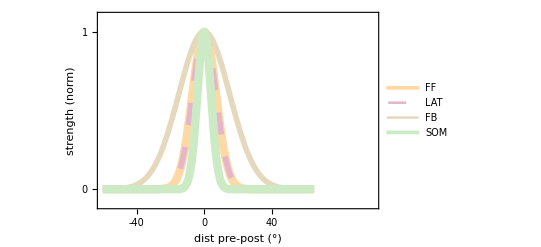

```mathematica
f1=Plot[{Exp[-x^2/(2 (Subscript[σ, AB][[1,5]])^2 )],Exp[-x^2/(2(Subscript[σ, AB][[1,1]])^2)],Exp[-x^2/(2(Subscript[σ, AB][[1,6]])^2)],Exp[-x^2/(2(Subscript[σ, AB][[1,3]])^2)]},{x,-60,65},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,(*PlotLabel->Style["connections",40,Darker[Gray]],*)FrameLabel->{{Style["strength
(norm)",30,Darker[Gray]],None},{Style["dist pre-post (°)",30,Darker[Gray]],None}},PlotRange->{{-60,100},{-.1,1.1}},FrameTicks->{{{0,1},None},{{-40,0,40},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotStyle->{{Thickness[0.015],colors[[5]]},{Thickness[0.01],colors[[7]],Dashing[{0.04,0.04}]},{Thickness[0.01],colors[[6]]},{Thickness[0.015],colors[[3]]}},PlotLegends->Placed[LineLegend[{"FF","LAT","FB","SOM"},LabelStyle->{GrayLevel[0.3],20}],{0.8,0.6}]]
```

# CLASSICAL STIMULI

## Rate fields and fits classical

```mathematica
aa=7;
stimstart=1;stimend=9;
stimname="direct";
ctns={"Pyr","PV","SOM","VIP","Scnn1","LMaxons","PyrPv"};
ctns2={"Pyr","PV","SOM","VIP","L4","LM","Pyr+PV"};
sizs={0,5,15,25,35,45,55,65,75,85};
Subscript[σdat, A]=
Import[StringJoin[{NotebookDirectory[],"/sigmasprefit_",stimname,"+.csv"}],"Data"];
halffield=Import[StringJoin[{NotebookDirectory[],"/spacetFR_",ctns[[aa]],".csv"}],"Data"];
field=Join[Reverse[halffield,2],halffield,2];
cents=Join[{0},Table[halffield[[i,1]]-halffield[[i,180]],{i,stimstart,stimend}]];
fieldsub=Table[field[[i]]-field[[i,1]],{i,stimstart,stimend}];parErffitd=Import[FileNameJoin[{NotebookDirectory[],"parameters_sizetunings_direct+.csv"}]];
tabd=parErffitd[[;;,4;;7]];
bd=Join[parErffitd[[;;,1]],{0}];
kdc=parErffitd[[;;,2]];(*THESE ARE IN DEGREES*)
kd=parErffitd[[;;,3]];
Subscript[rd, A][s_]:=Join[Table[tabd[[b,1]]Erf[s/tabd[[b,3]]]-tabd[[b,2]]Erf[s/tabd[[b,4]]],{b,1,7}],{Sqrt[s]}];
σ[s_]:=Join[Table[kd[[b]] s+kdc[[b]],{b,1,7}],{kd[[1]] s+kdc[[1]]}];
Subscript[σ2, ABp][s_]:=Table[(Subscript[σ, AB][[a,b]])^2+(σ[s][[b]])^2,{a,1,4},{b,1,7}];
noconfidence=Flatten[Import[StringJoin[{NotebookDirectory[],"spacetFR_maxdists+.csv"}],"Data"]];
```

```mathematica
tickf1={{0,1},{0,2,4},{0,3},{0,0.8},{0,0.8},{0,0.8},{0,1}};
pltrang1={{-.15,1.4},{-0.5,4.6},{-0.25,3.6},{-0.35,1},{-0.15,.9},{-0.05,1.1},{-0.7,1.7}};
pltrang1={{-.55,1.4},{-0.75,4.6},{-0.25,3.6},{-0.45,1},{-0.15,.9},{-0.05,1.1},{-0.1,1.7}};
```

```mathematica
who:={"Pyr","PV","SOM","VIP","L4","HVA","L2/3","input layer"};
```

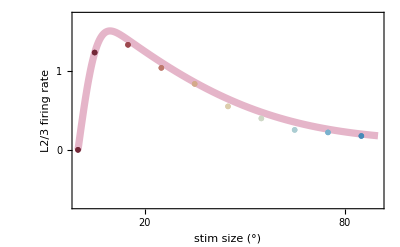

```mathematica
stepsiz=1;
optionsf1:={PlotRange->pltrang1[[aa]],PlotStyle->{Thickness[0.013],colors[[aa]]},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style[StringJoin[who[[aa]]," firing rate"],30,Darker[Gray]],None},{Style["stim size (°)",30,Darker[Gray]],None}},FrameTicks->{{tickf1[[aa]],None},{{20,80},None}},FrameTicksStyle->Directive[30,Darker[Gray]]};
f1=Show[{Plot[Subscript[rd, A][s][[aa]],{s,0,90},Evaluate[optionsf1]],ListPlot[Table[{{sizs[[i]],cents[[i]]}},{i,1,10}],PlotStyle->ColorData[colorgrads[[aa]]]/@Join[{0},Range[0,9]/9],PlotMarkers->{●,20}],ListPlot[Table[{{sizs[[sz+1]],Subscript[σdat, A][[aa,sz]]}},{sz,1,9,stepsiz}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf1]]}]
```

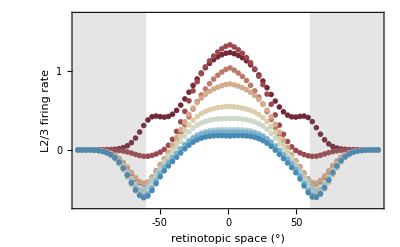

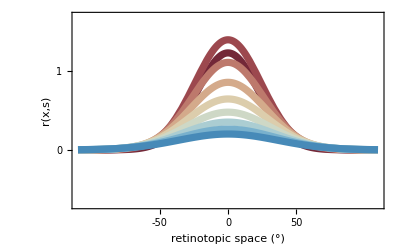

```mathematica
sizs={5,15,25,35,45,55,65,75,85};
xmin=70;
xmax=360-xmin;
stepsiz=1;
optionsf2:={PlotRange->pltrang1[[aa]],Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]stepsiz/9),Method->"DefaultPlotStyle"->Thickness[0.013],FrameLabel->{{Style[StringJoin[who[[aa]]," firing rate"],30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},FrameTicks->{{tickf1[[aa]],None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]](*,ImageSize->Large*)};
optionsf2list:={PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]stepsiz/9),PlotMarkers->{●,14},DataRange->{-180+xmin,-180+xmax}};
f2=Show[{ListPlot[Table[fieldsub[[sz,xmin;;xmax;;3]],{sz,1,9,stepsiz}],Evaluate[optionsf2],Evaluate[optionsf2list]],Plot[14,{x,-200,-noconfidence[[aa]]},Filling->-1,PlotStyle->Gray],Plot[14,{x,noconfidence[[aa]],200},Filling->-1,PlotStyle->Gray]}]
f2f=Plot[Evaluate@Table[Subscript[rd, A][sizs[[sz]]][[aa]]Exp[-x^2/(2(σ[sizs[[sz]]][[aa]])^2)],{sz,1,9,stepsiz}],{x,-180+xmin,-180+xmax},FrameLabel->{{Style["r(x,s)",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},Evaluate[optionsf2]]
```

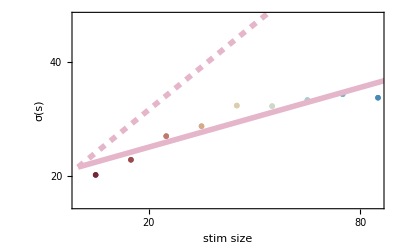

```mathematica
sizs={0,5,15,25,35,45,55,65,75,85};
optionsf3:={PlotRange->pltrangsigma[[aa]],Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,
FrameLabel->{{Style["σ(s)",30,Darker[Gray]],None},{Style["stim size",30,Darker[Gray]],None}},FrameTicks->{{ticksigma[[aa]],None},{{20,80},None}},FrameTicksStyle->Directive[30,Darker[Gray]]};
f3=Show[{ListPlot[Table[{{sizs[[sz+1]],Subscript[σdat, A][[aa,sz]]}},{sz,1,9,stepsiz}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf3]],Plot[{σ[s][[aa]],σ[0][[aa]]+s/2},{s,0,90},PlotStyle->{{colors[[aa]],Thickness[0.01]},{colors[[aa]],Thickness[0.01],Dashed}}]}]
```

## Conceptual model with inputs from L4&LM&SOM

```mathematica
G[x_,y_,σ_]:=Exp[-(x^2+y^2)/(2σ)]/(2π σ);
barσFB[s_]:=(k1+k2 s)^2;
barσRECI[s_]:=(k3+k4 s)^2;
σFF=σL4+barσFF;(*input from L4, after convolution*)
σFB[s_]:=σLM+barσFB[s];(*input from LM, after convolution*)
σRECI[s_]:=σSOM+barσRECI[s];(*input from SOM, after convolution*)
r0FF[s_]:=rff (Erf[s/S1]-ssL4 Erf[s/S2]);
r0FB[s_]:=rfb (Erf[s/S3]-ssLM Erf[s/S4]);
r0RECI[s_]:=rsom(Erf[s/S5]-ssSOM Erf[s/S6]);
rFF[x_,y_,s_]:=CFF r0FF[s]Exp[-(x^2+y^2)/(2barσFF)];
rFB[x_,y_,s_]:=CFB r0FB[s]Exp[-(x^2+y^2)/(2barσFB[s])];
rRECI[x_,y_,s_]:=CRECI r0RECI[s]Exp[-(x^2+y^2)/(2barσRECI[s])];
i0FF[s_]:=CFF WFF r0FF[s]2π barσFF;
i0FB[s_]:=CFB WFB r0FB[s]2π barσFB[s];
i0RECI[s_]:=CRECI WRECI r0RECI[s]2π barσRECI[s];
σ12FB[s_]:=σFF σFB[s]/(σFF-σFB[s]);
σ12RECI[s_]:=σFF σRECI[s]/(σFF-σRECI[s]);
σv=-σr+√(4 σFF σr+σr^2);
σrv=σv/2+σr;
uD[x_,y_,s_]:=(π (σFF+σrv) G[x,y,σFF])/w0(1-√(1-2i0FF[s] w0/(π(σFF+σrv))-4 σFF^2 w0((i0RECI[s]G[x,y,σ12RECI[s]])/((σFF-σRECI[s])(σFF + σrv))+(i0FB[s]G[x,y,σ12FB[s]])/((σFF-σFB[s])(σFF+σrv)))));
frD[x_,y_,s_]:=Piecewise[{{uD[x,y,s]^2,uD[x,y,s]>0}},0];
σ12[s_]:=σFF σFB[s]/(σFF-σFB[s]);
frL[x_,y_,s_]:=(σr G[x,y,σFF] (i0FF[s] (σFF-σFB[s])+2 i0FB[s] π σFF^2 G[x,y,σ12[s]]))/((σFF-σFB[s]) (σr+2 π σFF^2 w0 G[x,y,-(σFF (σFF+σr))/σr]));(*this is the linear solution when the input are LM and L4*)
```

## Compare analytics (SOM input=0) with simulations

```mathematica
frdata=Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/sizetuningcurve_Pyr_1.csv"}],"Data"]];
profdata=Table[Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/spatialprofiles_Pyr_Dirsiz",ToString[ssim],"_1.csv"}],"Data"]],{ssim,5,90,10}];
ssiz=Table[ssim,{ssim,5,90,10}];
Nn=60;
dx2deg=6;
```

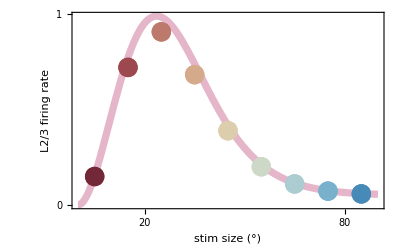

```mathematica
aa=7;
parD={σr->(Subscript[σ, AB][[1,1]])^2,σLM->(Subscript[σ, AB][[1,6]])^2,σL4->(Subscript[σ, AB][[1,5]])^2,σSOM->(Subscript[σ, AB][[1,3]])^2,w0->-.4,WFF->1,WRECI->-0.15,WFB->.75,CFF->1,CFB->1,CRECI->1};
parDLM={rfb->tabd[[6,1]],k1->kdc[[6]],k2->kd[[6]],ssLM->tabd[[6,2]]/tabd[[6,1]],S3->tabd[[6,3]],S4->tabd[[6,4]]};
parDL4={rff->tabd[[5,1]],ssL4->tabd[[5,2]]/tabd[[5,1]],S1->tabd[[5,3]],S2->tabd[[5,4]],barσFF->kdc[[5]]^2};
parDSOM={rsom->tabd[[3,1]],ssSOM->tabd[[3,2]]/tabd[[3,1]],k3->kdc[[3]],k4->kd[[3]],S5->tabd[[3,3]],S6->tabd[[3,4]]};
parNOSOM=WRECI->-0.;
f1=Show[{Plot[frD[0,0,s]/.parNOSOM/.parDSOM/.parD/.parDLM/.parDL4,{s,0,90},PlotRange->All,Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"analyt"},LabelStyle->{GrayLevel[0.3],26}],{0.75,0.75}]],ListPlot[Table[{{ssiz[[s]],frdata[[s]]}},{s,1,Length[frdata]}],PlotMarkers->{"●",20},PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotLegends->Placed[LineLegend[{"simulat"},LabelStyle->{GrayLevel[0.3],26}],{0.75,0.75}]]}]
```

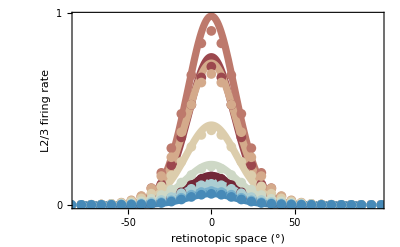

```mathematica
xmin=100;
xmax=370-xmin;
f2=Show[{Plot[Evaluate@Table[frD[x,0,s]/.parNOSOM/.parDSOM/.parD/.parDLM/.parDL4,{s,5,90,10}],{x,-180+xmin,-180+xmax},PlotRange->{{-180+xmin,-180+xmax+10},All},Evaluate[optionsf2],PlotLegends->Placed[LineLegend[{"analyt"},LabelStyle->{GrayLevel[0.3],24}],{0.75,0.75}]],ListPlot[Table[Table[{-Nn dx2deg/2+dx2deg x,profdata[[s,x]]},{x,0,Nn}],{s,1,Length[frdata]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{"●",10},PlotLegends->Placed[LineLegend[{"simulat"},LabelStyle->{GrayLevel[0.3],24}],{0.75,0.75}]]}]
```

## Dependence on parameters

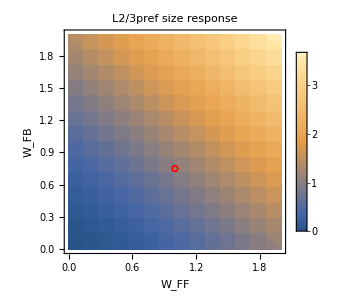

```mathematica
optionsdensity:={FrameLabel->{{Style["W_FB",20,Darker[Gray]],None},{Style["W_FF",20,Darker[Gray]],None}},FrameTicksStyle->Directive[20,Darker[Gray]],ImageSize->300,PlotLabel->StringJoin[who[[aa]],"pref size response"],LabelStyle->Directive[20,Darker[Gray]]};
dp=Show[DensityPlot[frD[0,0,25]/.{WFF->wff,WFB->wfb}/.parNOSOM/.parDSOM/.parD/.parDLM/.parDL4,{wff,0,2},{wfb,0,2},PlotLegends->Automatic,Evaluate[optionsdensity]],ListPlot[{{WFF,WFB}}/.parD,PlotMarkers->{○,18},PlotStyle->Red]]
```

## Opto stimulation/silencing of PV

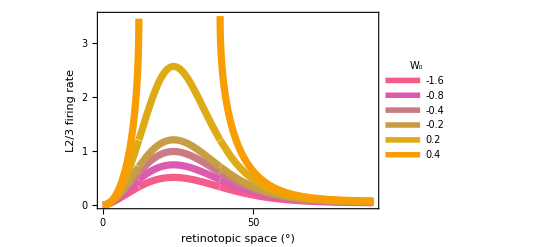

```mathematica
optionsfpv:={PlotRange->pltrang1[[aa]],Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,PlotStyle->ColorData[{"FruitPunchColors","Reverse"}]/@(Range[0,6]/6),Method->"DefaultPlotStyle"->Thickness[0.013],FrameLabel->{{Style["L2/3 firing rate",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},FrameTicks->{{{0,1,2,3},None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]](*,ImageSize->Large*)};
f1=Plot[Evaluate@Table[frD[0,0,s]/.parNOSOM/.parDSOM/.w0->W0/.parD/.parDLM/.parDL4,{W0,{-1.6,-.8,-.4,-.2,.2,.4}}],{s,0,90},PlotRange->All,Evaluate[optionsfpv],PlotLegends->Placed[LineLegend[{"-1.6","-0.8","-0.4","-0.2","0.2","0.4"},LabelStyle->{GrayLevel[0.3],22},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18,LegendLabel->"W_0"],{0.83,0.485}]]
```

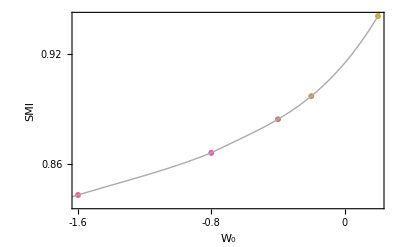

```mathematica
largesize=65;
SMI=1-(Table[frD[0,0,largesize]/.parNOSOM/.parDSOM/.w0->W0/.parD/.parDLM/.parDL4,{W0,{-1.6,-.8,-.4,-.2,.2}}])/Table[MaxValue[frD[0,0,s]/.parNOSOM/.parDSOM/.w0->W0/.parD/.parDLM/.parDL4,s],{W0,{-1.6,-.8,-.4,-.2,.2}}];
W0s={-1.6,-.8,-.4,-.2,.2};
finterpol=Interpolation[Table[{W0s[[i]],SMI[[i]]},{i,1,Length[SMI]}]];
f2=Show[{ListPlot[Table[{{W0s[[i]],SMI[[i]]}},{i,1,Length[SMI]}],PlotRange->All,PlotMarkers->●,FrameLabel->{{Style["SMI",30,Darker[Gray]],None},{Style["W_0",30,Darker[Gray]],None}},FrameTicks->{{{0.86,0.92},None},{{-1.6,-0.8,0},None}},Evaluate[optionsfpv]],Quiet[Plot[finterpol[x],{x,-2,0.5},PlotStyle->{Lighter[Gray],Thick}]]}]
```

```mathematica
(*see Nienborg et al 2013*)
```

## Modifiers on LM

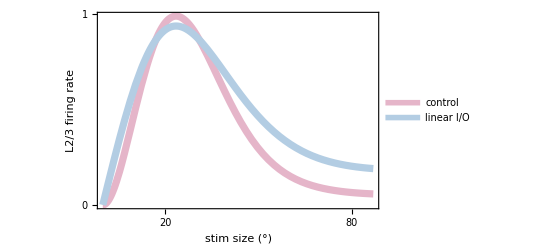

```mathematica
f1=Plot[{frD[0,0,s]/.parNOSOM/.parDSOM/.parD/.parDLM/.parDL4,frL[0,0,s]/.parNOSOM/.parDSOM/.parD/.parDLM/.parDL4},{s,0,87},PlotRange->All,PlotStyle->{{colors[[aa]],Thickness[0.013]},{colors[[2]],Thickness[0.013]}},Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"control","linear I/O"},LabelStyle->{GrayLevel[0.3],20},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18],{0.3,0.3}]]
```

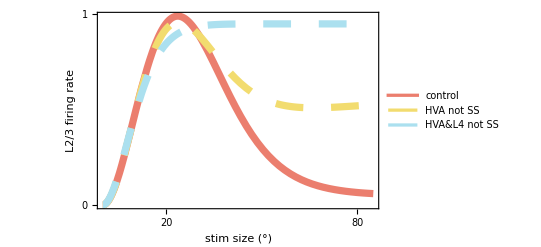

```mathematica
aa=7;
parDNOk2=k2->0.;
parDNOssLM={rfb->1.1,ssLM->0,S3->18};
parDNOssLMNOssL4={rfb->1.1,ssLM->0.,S3->18,rff->0.85,ssL4->0.,S1->13,k2->0};
parDNOssL4={rff->0.85,ssL4->0,S1->13};
f1=Plot[{frD[0,0,s]/.parNOSOM/.parDSOM/.parD/.parDLM/.parDL4,frD[0,0,s]/.parNOSOM/.parDSOM/.parD/.parDNOssLM/.parDLM/.parDL4,frD[0,0,s]/.parNOSOM/.parDSOM/.parD/.parDNOssLMNOssL4/.parDLM/.parDL4},{s,0,85},PlotRange->All,PlotStyle->{{(*colors[[aa]]*)ColorData[24]@1,Thickness[0.013]},{(*Lighter[Black]*)ColorData[24]@3,Thickness[0.013],Dashing[{0.05,0.05}]},{(*Lighter[Lighter[Gray]]*)ColorData[24]@4,Thickness[0.013],Dashing[{0.05,0.05}]}},Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"control","HVA not SS","HVA&L4 not SS"},LabelStyle->{GrayLevel[0.3],20},Spacings->0.18],{0.44,0.2}]]
```

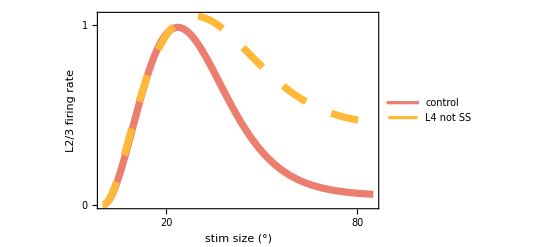

```mathematica
f1=Plot[{frD[0,0,s]/.parNOSOM/.parDSOM/.parD/.parDLM/.parDL4,frD[0,0,s]/.parNOSOM/.parDSOM/.parD/.parDNOssL4/.parDLM/.parDL4},{s,0,85},PlotRange->All,PlotStyle->{{(*colors[[aa]]*)ColorData[24]@1,Thickness[0.013]},{(*Lighter[Lighter[Gray]]*)ColorData[24]@2,Thickness[0.013],Dashing[{0.05,0.05}]}},Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"control","L4 not SS"},LabelStyle->{GrayLevel[0.3],20},Spacings->0.18],{0.38,0.18}]]
```

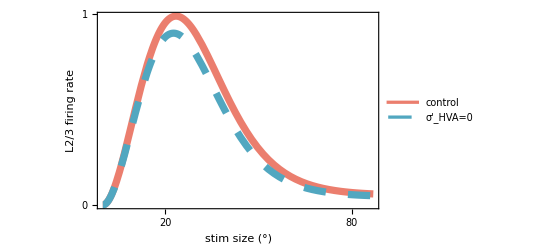

```mathematica
aa=7;
parDNOk2=k2->0.;
parDlargerk2=k2->0.5;
parDNOssLM={rfb->1.1,ssLM->0,S3->18};
f1=Plot[{frD[0,0,s]/.parNOSOM/.parDSOM/.parD/.parDLM/.parDL4,frD[0,0,s]/.parNOSOM/.parDSOM/.parD/.parDNOk2/.parDLM/.parDL4},{s,0,87},PlotRange->All,PlotStyle->{{ColorData[24]@1,Thickness[0.013]},{ColorData[24]@5,Thickness[0.013],Dashing[{0.04,0.04}]},{Black,Dashing[{0.02,0.02}],Thickness[0.013]}},Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"control","σ'_HVA=0"},LabelStyle->{GrayLevel[0.3],20},Spacings->0.18],{0.33,0.2}]]
```

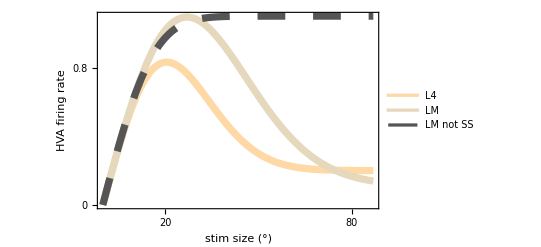

```mathematica
f2=Plot[{r0FF[s]/.parD/.parDLM/.parDL4,r0FB[s]/.parD/.parDLM/.parDL4,r0FB[s]/.parD/.parDNOssLM/.parDLM/.parDL4},{s,0,87},PlotRange->All,PlotStyle->{{colors[[5]],Thickness[0.013]},{colors[[6]],Thickness[0.013]},{Lighter[Black],Thickness[0.013],Dashing[{0.05,0.05}]}},Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"L4","LM","LM not SS"},LabelStyle->{GrayLevel[0.3],22},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18],{0.35,0.35}]]
```

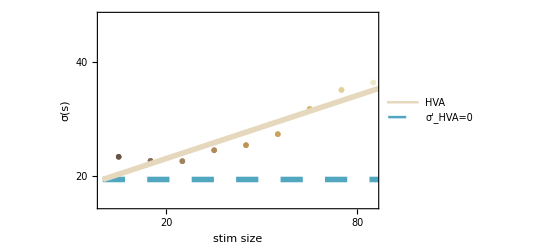

```mathematica
aa=6;
f3=Show[{ListPlot[Table[{{sizs[[sz+1]],Subscript[σdat, A][[aa,sz]]}},{sz,1,9,stepsiz}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf3]],Plot[{σ[s][[aa]](*,σ[0][[aa]]+s/2*),σ[0][[aa]]},{s,0,90},PlotStyle->{{colors[[aa]],Thickness[0.01]},(*{Black,Thickness[0.01],Dashing[{0.04,0.04}]},*){(*ColorData[24]@7*)ColorData[24]@5,Thickness[0.01],Dashing[{0.04,0.04}]}},PlotLegends->Placed[LineLegend[{"HVA","σ'_HVA=0","σ'_HVA=0.5"},LabelStyle->{GrayLevel[0.3],22},LegendFunction->(Framed[#,FrameMargins->0,Background->White,FrameStyle->White]&),Spacings->0.18],{0.29,0.75}]]}]
```

## SMI and modifiers

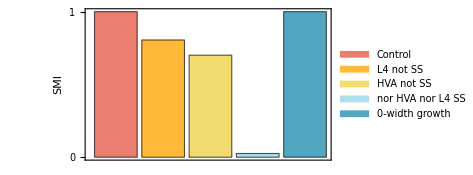

{1.,0.80546,0.701072,0.0255584,1.}

```mathematica
(*measure of SMI*)
(*I am considering the system WITH SOM*)
largesize=85;
SMIctrl=1-(frD[0,0,largesize]/.parDSOM/.parD/.parDLM/.parDL4)/MaxValue[frD[0,0,s]/.parDSOM/.parD/.parDLM/.parDL4,s];
SMINOSOM=1-(frD[0,0,largesize]/.parNOSOM/.parDSOM/.parD/.parDLM/.parDL4)/MaxValue[frD[0,0,s]/.parNOSOM/.parDSOM/.parD/.parDLM/.parDL4,s];
SMINOssLM=1-(frD[0,0,largesize]/.parDNOssLM/.parDSOM/.parD/.parDLM/.parDL4)/MaxValue[frD[0,0,s]/.parDNOssLM/.parDSOM/.parD/.parDLM/.parDL4,s];
SMINOssL4=1-(frD[0,0,largesize]/.parDNOssL4/.parDSOM/.parD/.parDLM/.parDL4)/MaxValue[frD[0,0,s]/.parDNOssL4/.parDSOM/.parD/.parDLM/.parDL4,s];
SMINOssLMNOssL4=1-(frD[0,0,largesize]/.parDNOssLMNOssL4/.parDSOM/.parD/.parDLM/.parDL4)/MaxValue[frD[0,0,s]/.parDNOssLMNOssL4/.parDSOM/.parD/.parDLM/.parDL4,s];
SMINOk2=1-(frD[0,0,largesize]/.parDNOk2/.parDSOM/.parD/.parDLM/.parDL4)/MaxValue[frD[0,0,s]/.parDNOk2/.parDSOM/.parD/.parDLM/.parDL4,s];
parDNOLM={CFB->0};
SMINOLM=1-(frD[0,0,largesize]/.parDNOLM/.parDSOM/.parD/.parDLM/.parDL4)/MaxValue[frD[0,0,s]/.parDNOLM/.parDSOM/.parD/.parDLM/.parDL4,s];
parDNOL4={CFF->0};
SMINOL4=1-(frD[0,0,largesize]/.parDNOL4/.parDSOM/.parD/.parDLM/.parDL4)/MaxValue[frD[0,0,s]/.parDNOL4/.parDSOM/.parD/.parDLM/.parDL4,s];
bc=BarChart[{{SMIctrl,SMINOssL4,SMINOssLM,SMINOssLMNOssL4,SMINOk2}},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["SMI",27,Darker[Gray]],None},{None,None}},FrameTicks->{{{0,1},None},{None,None}},FrameTicksStyle->Directive[30,Darker[Gray]],AspectRatio->1/2,ImageSize->350,ChartStyle->24,ChartLegends->{"Control","L4 not SS","HVA not SS","nor HVA nor L4 SS","0-width growth" },LabelStyle->{GrayLevel[0.3],22}]
{SMIctrl,SMINOssL4,SMINOssLM,SMINOssLMNOssL4,SMINOk2}
```

## LM only input, LM not surround suppressed but larger σ'_LM

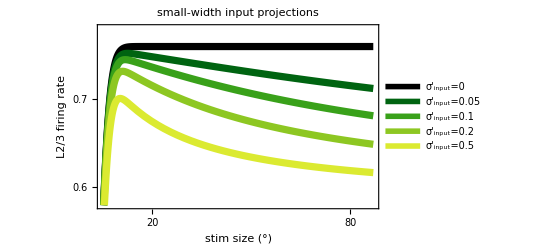

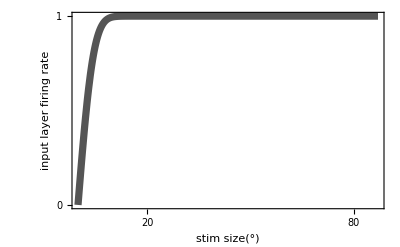

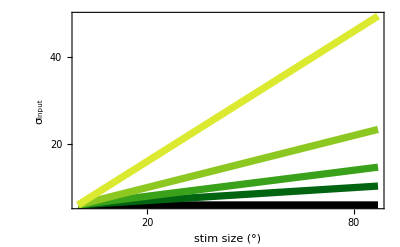

```mathematica
tickf1={{0,1},{0,2,4},{0,3},{0,0.8},{0,0.8},{0,0.8},{0,1}};
aa=7;
Clear[s]
parnoLM={rfb->0};
(*parDNOssL4largek2={σr->8^2,σL4->0.33^2,barσFF-> (6+k2 s)^2,rff->1,ssL4->0,w0->-30,WFF->6,S1->5};*)
parDNOssL4largek2={σr->7^2,σL4->1^2,barσFF->(6+k2 s)^2,rff->1,ssL4->0,w0->-0.4,WFF->1,S1->5};
f1=Plot[Evaluate@Table[frD[0,0,s]/.parNOSOM/.parDSOM/.parDNOssL4largek2/.{k2->K2}/.parD/.parnoLM/.parDLM/.parDL4,{K2,{0,0.05,0.1,0.2,0.5}}],{s,-10,87},PlotRange->{{5,87},{0.58,0.78}},PlotStyle->ColorData["AvocadoColors"]/@(Range[0,4]/4.5),Method->"DefaultPlotStyle"->Thickness[0.013],FrameTicks->{{{0.6,0.7},None},{{20,80},None}},PlotLabel->Style["small-width input projections",20,Darker[Gray]],Evaluate[optionsf1],PlotLegends->LineLegend[Table[StringJoin["σ'_input=",ToString[B2]],{B2,{0,0.05,0.1,0.2,0.5}}],LabelStyle->{GrayLevel[0.3],20}]]

f2=Plot[rFF[0,0,s]/.parDNOssL4largek2/.{k2->K2}/.parD/.parDL4,{s,0,87},PlotRange->All,FrameLabel->{{Style["input layer
 firing rate",30,Darker[Gray]],None},{Style["stim size(°)",30,Darker[Gray]],None}},PlotStyle->{Lighter[Black],Thickness[0.013]},Evaluate[optionsf1]]

f11=Plot[Evaluate@Table[Sqrt[barσFF]/.parDNOssL4largek2/.{k2->K2},{K2,{0,0.05,0.1,0.2,0.5}}],{s,0,87},PlotRange->All,PlotStyle->ColorData["AvocadoColors"]/@(Range[0,4]/4.5),Method->"DefaultPlotStyle"->Thickness[0.013],FrameLabel->{{Style["σ_input",30,Darker[Gray]],None},{Style["stim size (°)",30,Darker[Gray]],None}},FrameTicks->{{{20,40},None},{{20,80},None}},Evaluate[optionsf1]]
```

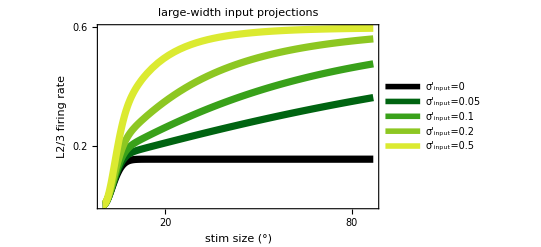

```mathematica
parDNOssL4largek2={σr->7^2,σL4->7^2,barσFF->(6+k2 s)^2,rff->1,ssL4->0,w0->-0.4,WFF->1,S1->5};
f1=Plot[Evaluate@Table[frD[0,0,s]/.parNOSOM/.parDSOM/.parDNOssL4largek2/.{k2->K2}/.parD/.parnoLM/.parDLM/.parDL4,{K2,{0,0.05,0.1,0.2,0.5}}],{s,0,87},PlotRange->All,PlotStyle->ColorData["AvocadoColors"]/@(Range[0,4]/4.5),Method->"DefaultPlotStyle"->Thickness[0.013],FrameTicks->{{{0.2,0.6},None},{{20,80},None}},PlotLabel->Style["large-width input projections",20,Darker[Gray]],Evaluate[optionsf1],PlotLegends->LineLegend[Table[StringJoin["σ'_input=",ToString[B2]],{B2,{0,0.05,0.1,0.2,0.5}}],LabelStyle->{GrayLevel[0.3],20}]]
```

## same as above, checking if by changing contrast the preferred size changes

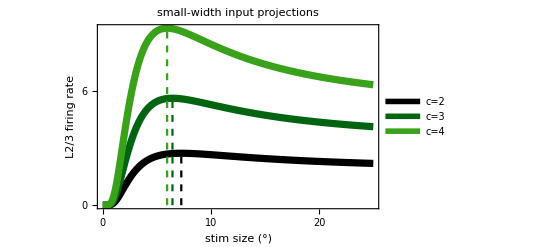

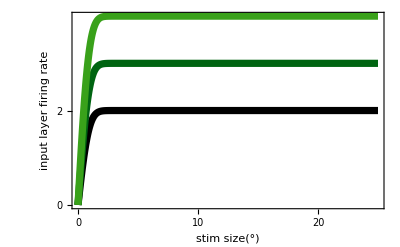

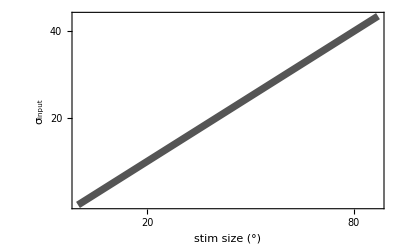

```mathematica
cntrsts={2,3,4};(*cntrsts={1.5,2,3};cntrsts={10,15,20};*)
tickf1={{0,4},{0,2,4},{0,3},{0,0.8},{0,0.8},{0,0.8},{0,2,4}};
aa=7;
Clear[c]
parnoLM={rfb->0};
parDNOssL4largek2={σr->7^2,σL4->1^2,barσFF->(0.5 s)^2,rff->c,ssL4->0,w0->-0.4,WFF->1,S1->1};
is=Table[ArgMax[{frD[0,0,s]/.parNOSOM/.parDSOM/.parDNOssL4largek2/.{c->ctrst}/.parD/.parnoLM/.parDLM/.parDL4,s>0},s],{ctrst,cntrsts}];
ms=Table[MaxValue[{frD[0,0,s]/.parNOSOM/.parDSOM/.parDNOssL4largek2/.{c->ctrst}/.parD/.parnoLM/.parDLM/.parDL4,s>0},s],{ctrst,cntrsts}];
f1=Show[{Plot[Evaluate@Table[frD[0,0,s]/.parNOSOM/.parDSOM/.parDNOssL4largek2/.{c->ctrst}/.parD/.parnoLM/.parDLM/.parDL4,{ctrst,cntrsts}],{s,0,25},PlotRange->All,PlotStyle->ColorData["AvocadoColors"]/@(Range[0,4]/4.5),Method->"DefaultPlotStyle"->Thickness[0.013],FrameTicks->{{{0,6},None},{{0,10,20},None}},PlotLabel->Style["small-width input projections",20,Darker[Gray]],Evaluate[optionsf1],PlotLegends->LineLegend[Table[StringJoin["c=",ToString[B2]],{B2,cntrsts}],LabelStyle->{GrayLevel[0.3],20}]],Table[ParametricPlot[{is[[i]],u},{u,0,ms[[i]]},PlotStyle->{ColorData["AvocadoColors"]@((i-1)/4.5),Thick,Dashed}],{i,1,3}]}]
f2=Plot[Evaluate@Table[rFF[0,0,s]/.parDNOssL4largek2/.{c->ctrst}/.parD/.parDL4,{ctrst,cntrsts}],{s,0,25},PlotRange->All,FrameLabel->{{Style["input layer
 firing rate",30,Darker[Gray]],None},{Style["stim size(°)",30,Darker[Gray]],None}},Method->"DefaultPlotStyle"->Thickness[0.013],PlotStyle->ColorData["AvocadoColors"]/@(Range[0,4]/4.5),FrameTicks->{{{0,2},None},{{0,10,20},None}},Evaluate[optionsf1]]

f11=Plot[Sqrt[barσFF]/.parDNOssL4largek2,{s,0,87},PlotRange->All,PlotStyle->{Lighter[Black],Thickness[0.013]},Method->"DefaultPlotStyle"->Thickness[0.013],FrameLabel->{{Style["σ_input",30,Darker[Gray]],None},{Style["stim size (°)",30,Darker[Gray]],None}},FrameTicks->{{{20,40},None},{{20,80},None}},Evaluate[optionsf1]]
```

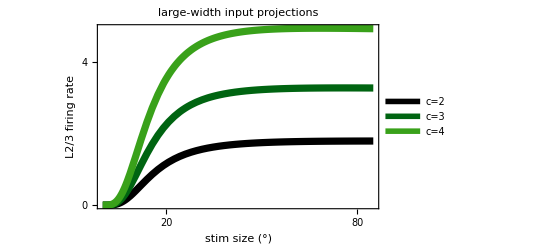

```mathematica
parDNOssL4largek2={σr->7^2,σL4->7^2,barσFF->(0.5 s)^2,rff->c,ssL4->0,w0->-0.4,WFF->1,S1->1};
f1=Plot[Evaluate@Table[frD[0,0,s]/.parNOSOM/.parDSOM/.parDNOssL4largek2/.{c->ctrst}/.parD/.parnoLM/.parDLM/.parDL4,{ctrst,cntrsts}],{s,0,85},PlotRange->All,PlotStyle->ColorData["AvocadoColors"]/@(Range[0,4]/4.5),Method->"DefaultPlotStyle"->Thickness[0.013],FrameTicks->{{{0,4},None},{{20,80},None}},PlotLabel->Style["large-width input projections",20,Darker[Gray]],Evaluate[optionsf1],PlotLegends->LineLegend[Table[StringJoin["c=",ToString[B2]],{B2,cntrsts}],LabelStyle->{GrayLevel[0.3],20}]]
```

## preferred size in between inputs preferred sizes

```mathematica
parDNOssL4largek2={σr->8^2,σL4->1^2,barσFF-> (0.5 s)^2,rff->c,ssL4->0,w0->-10,WFF->1,S1->1};
```

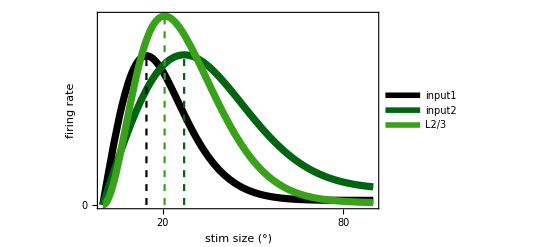

```mathematica
tickf1={{0,4},{0,2,4},{0,3},{0,0.8},{0,0.8},{0,0.8},{0,2,4}};
aa=7;
parDL4prefsize={rff->1.1,ssL4->0.99,S1->15,S2->30};
parDLMprefsize={k2->0,rfb->5.7};
parDnorm={WFF->1.,WFB->2.5};
is={ArgMax[{rFF[0,0,s]/.parD/.parDL4prefsize/.parDL4,s>0},s],ArgMax[{rFB[0,0,s]/.parD/.parDLMprefsize/.parDLM,s>0},s],ArgMax[{frD[0,0,s]/.parNOSOM/.parDSOM/.parDnorm/.parD/.parDL4prefsize/.parDLMprefsize/.parDLM/.parDL4,s>0},s]};
ms={MaxValue[{rFF[0,0,s]/.parD/.parDL4prefsize/.parDL4,s>0},s],MaxValue[{rFB[0,0,s]/.parD/.parDLMprefsize/.parDLM,s>0},s],MaxValue[{frD[0,0,s]/.parNOSOM/.parDSOM/.parDnorm/.parD/.parDL4prefsize/.parDLMprefsize/.parDLM/.parDL4,s>0},s]};
f1=Show[{Plot[{rFF[0,0,s]/.parD/.parDL4prefsize/.parDL4,rFB[0,0,s]/.parD/.parDLMprefsize/.parDLM,frD[0,0,s]/.parNOSOM/.parDSOM/.parDnorm/.parD/.parDL4prefsize/.parDLMprefsize/.parDLM/.parDL4},{s,0,90},PlotRange->All,PlotStyle->ColorData["AvocadoColors"]/@(Range[0,4]/4.5),Method->"DefaultPlotStyle"->Thickness[0.013],FrameLabel->{{Style["firing rate",30,Darker[Gray]],None},{Style["stim size (°)",30,Darker[Gray]],None}},Evaluate[optionsf1],PlotLegends->LineLegend[{"input1","input2","L2/3"},LabelStyle->{GrayLevel[0.3],20}]],Table[ParametricPlot[{is[[i]],u},{u,0,ms[[i]]},PlotStyle->{ColorData["AvocadoColors"]@((i-1)/4.5),Thick,Dashed}],{i,1,3}]}]
```

## Compare Mario’s data with analytics (SOM input≠0) and simulations

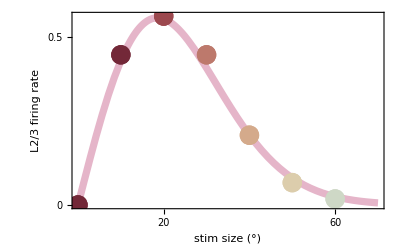

```mathematica
(*Mario's data*)
halffield=Import[StringJoin["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/SSNdoc/the_path_to_the_hole/Data/mario_size_tuning_data/spacetM_FR3",ctns[[aa]],".csv"],"Data"];
field=Join[Reverse[halffield,2],halffield,2];
cents=Table[halffield[[i,1]]-halffield[[i,180]],{i,1,10}];sizs={0,5,10,15,20,25,30,40,50,60};
indx={1,3,5,7,8,9,10};
fieldsub=Table[field[[i]]-field[[i,1]],{i,1,10}];
f1=Show[{Plot[3.1(Erf[s/22]-Erf[s/32]),{s,0,70},PlotRange->All,FrameTicks->{{{0,0.5},None},{{20,60},None}},Evaluate[optionsf1]],ListPlot[Table[{{sizs[[indx[[i]]]],cents[[indx[[i]]]]}},{i,1,Length[indx]}],PlotStyle->ColorData[colorgrads[[aa]]]/@Join[{0},Range[0,9]/9],PlotMarkers->{"●",20}]}]
```

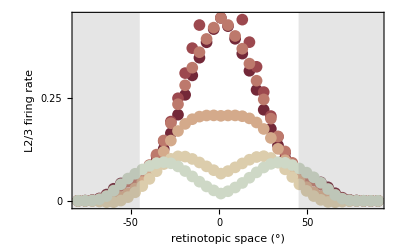

```mathematica
optionsf2M={PlotRange->{-.01,.45},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{"●",12},DataRange->{-180+xmin,-180+xmax},FrameLabel->{{Style["L2/3 firing rate",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},FrameTicks->{{{0,0.25},None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]]};
f2=Show[{ListPlot[Table[fieldsub[[indx[[i]],xmin;;xmax;;4]],{i,2,Length[indx]}],Evaluate[optionsf2M]],Plot[14,{x,-200,-45},Filling->-1,PlotStyle->Gray],Plot[14,{x,45,200},Filling->-1,PlotStyle->Gray]}]
```

```mathematica
frdataS=Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/sizetuningcurve_Pyr_2.csv"}],"Data"]];
profdataS=Table[Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/spatialprofiles_Pyr_Dirsiz",ToString[ssim],"_2.csv"}],"Data"]],{ssim,{5,15,22,30,40,50,60}}];
ssiz=Table[ssim,{ssim,{5,15,22,30,40,50,60}}];
Nn=60;
dx2deg=6;
```

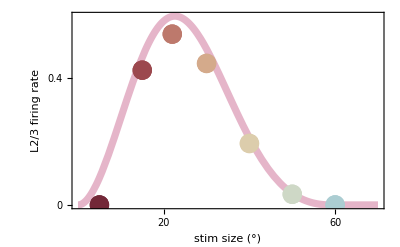

```mathematica
aa=7;
f1=Show[{Plot[1.2frD[0,0,s]/.parD/.parDLM/.parDL4/.parDSOM,{s,0,70},PlotRange->All,FrameTicks->{{{0,0.4},None},{{20,60},None}},Evaluate[optionsf1],
PlotLegends->Placed[LineLegend[{"analyt"},LabelStyle->{GrayLevel[0.3],26}],{0.75,0.75}]],ListPlot[Table[{{ssiz[[s]],1.2frdataS[[s]]}},{s,1,7}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{"●",20},PlotLegends->Placed[LineLegend[{"simulat"},LabelStyle->{GrayLevel[0.3],26}],{0.75,0.75}]]}]
```

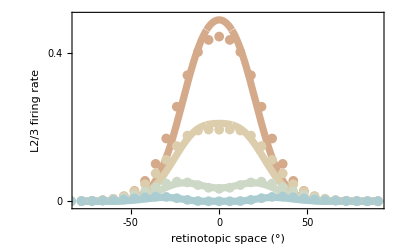

```mathematica
xmin=100;
xmax=370-xmin;
optionsf2Mp={PlotRange->{-.01,.5},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[3,9]/9),Method->"DefaultPlotStyle"->Thickness[0.013],FrameLabel->{{Style["L2/3 firing rate",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},FrameTicks->{{{0,0.4},None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]]};
optionsf2M={PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[3,9]/9),PlotMarkers->{"●",10},DataRange->{-180+xmin,-180+xmax}};
f2=Show[{Plot[Evaluate@Table[1.2frD[x,0,s]/.parD/.parDLM/.parDL4/.parDSOM,{s,{30,40,50,60}}],{x,-180+xmin,-180+xmax},Evaluate[optionsf2Mp]],ListPlot[Table[Table[{-Nn dx2deg/2+dx2deg x,1.2profdataS[[s,x]]},{x,0,Nn}],{s,4,7}],Evaluate[optionsf2M]]}]
```

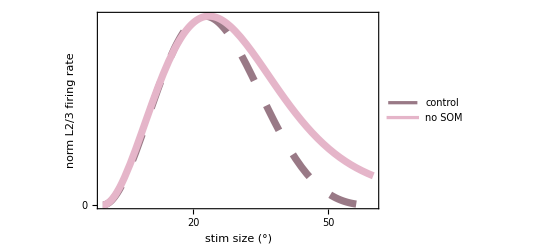

```mathematica
aa=7;
m1=MaxValue[frD[0,0,s]/.parD/.parDL4/.parDLM/.parDSOM,s];
m2=MaxValue[frD[0,0,s]/.parNOSOM/.parD/.parDL4/.parDLM/.parDSOM,s];
optionsf1mod:={PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["norm L2/3 firing rate",30,Darker[Gray]],None},{Style["stim size (°)",30,Darker[Gray]],None}},FrameTicks->{{tickf1[[aa]],None},{{20,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotLegends->Placed[LineLegend[{"control","no SOM"},LabelStyle->{GrayLevel[0.3],22},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.3,0.3}]};
f5=Plot[{frD[0,0,s]/m1/.parD/.parDL4/.parDLM/.parDSOM,frD[0,0,s]/m2/.parNOSOM/.parD/.parDL4/.parDLM/.parDSOM},{s,0,60},PlotStyle->{{Thickness[0.013],Darker[colors[[aa]]],Dashing[{0.05,0.05}]},{Thickness[0.013],colors[[aa]]}},Evaluate[optionsf1mod]]
```

## Optogenetic Silencing of LM

```mathematica
frdataSil=Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/sizetuningcurve_Pyr_3.csv"}],"Data"]];
ssiz=Table[ssim,{ssim,5,90,10}];
Nn=60;
dx2deg=6;
```

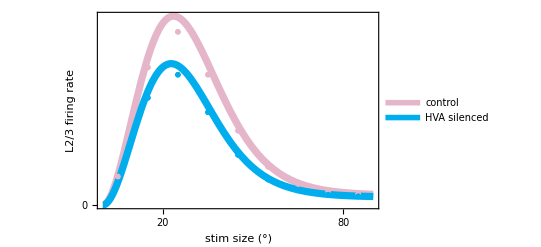

```mathematica
aa=7;
parDLMsil=CFB->0.65;
f1=Show[{Plot[{frD[0,0,s]/.parNOSOM/.parD/.parDLM/.parDL4/.parDSOM,frD[0,0,s]/.parNOSOM/.parDLMsil/.parD/.parDLM/.parDL4/.parDSOM},{s,0,90},PlotRange->All,PlotStyle->{{colors[[aa]],Thickness[0.013]},{RGBColor[0,173/255,237/255],Thickness[0.013]}},Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"control","HVA silenced"},LabelStyle->{GrayLevel[0.3],20},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18],{0.7,0.75}]],ListPlot[Table[{{ssiz[[s]],frdata[[s]]}},{s,1,Length[frdata]}],PlotStyle->colors[[aa]],PlotMarkers->{●,20}],ListPlot[Table[{{ssiz[[s]],frdataSil[[s]]}},{s,1,Length[frdataSil]}],PlotStyle->RGBColor[0,173/255,237/255],PlotMarkers->{●,20}]}]
```

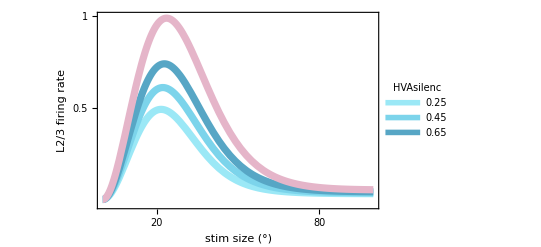

```mathematica
f1=Show[{Plot[Evaluate@Table[frD[0,0,s]/.{CFB->cfb}/.parNOSOM/.parD/.parDLM/.parDL4/.parDSOM,{cfb,{0.25,0.45,0.65}}],{s,0,100},PlotRange->{-0.03,1.},PlotStyle->ColorData["BrownCyanTones"]/@(Range[7,9]/9),Method->"DefaultPlotStyle"->Thickness[0.013],FrameTicks->{{{0.5,1},None},{{20,80},None}},Evaluate[optionsf1],
PlotLegends->Placed[LineLegend[Table[ToString[cfb],{cfb,{0.25,0.45,0.65}}],LabelStyle->{GrayLevel[0.3],20},LegendLabel->"HVAsilenc",LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18],{0.78,0.67}]],Plot[frD[0,0,s]/.parNOSOM/.parD/.parDLM/.parDL4/.parDSOM,{s,0,100},PlotStyle->{colors[[7]],Thickness[0.013]}]}]
```

## Contrast

```mathematica
cntrst={0.6,0.7,0.8,0.9,1.};
truecntrst=Log2[2cntrst];
resptolarge=frD[0,0,80]/.parNOSOM/.parD/.parDLM/.parDL4/.parDSOM;
SMI=1-Table[(resptolarge/frD[0,0,20]/.{CFF->c,CFB->c})/.parNOSOM/.parD/.parDLM/.parDL4/.parDSOM,{c,cntrst}];
SMI=SMI/SMI[[Length[SMI]]];
```

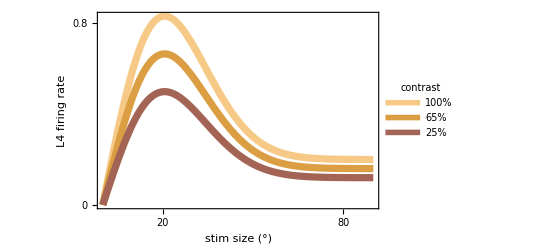

```mathematica
aa=5;
f1i=Plot[{r0FF[s]/.parD/.parDL4,0.8r0FF[s]/.parD/.parDL4,0.6r0FF[s]/.parD/.parDL4},{s,0,90},PlotRange->All,Method->"DefaultPlotStyle"->Thickness[0.013],PlotStyle->ColorData[17]/@{5,4,3},FrameTicks->{{tickf1[[4]],None},{{20,80},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotLegends->Placed[LineLegend[{"100%","65%","25%"},LabelStyle->{GrayLevel[0.3],20},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18,LegendLabel->"contrast"],{0.8,0.67}],Evaluate[optionsf1]]
```

```mathematica
resptolargeL=frL[0,0,80]/.parNOSOM/.parD/.parDLM/.parDL4/.parDSOM;
SMIL=Table[(((frL[0,0,80]/frL[0,0,20])/.{CFF->c,CFB->c})/((frL[0,0,80]/frL[0,0,20])/.{CFF->cntrst[[1]],CFB->cntrst[[1]]}))/.parNOSOM/.parD/.parDLM/.parDL4/.parDSOM,{c,cntrst}];
```

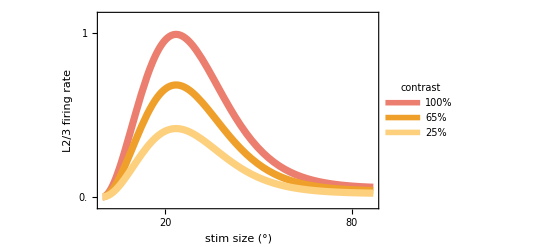

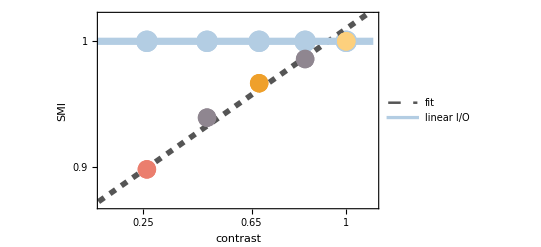

```mathematica
aa=7;
f1=Plot[{frD[0,0,s]/.parNOSOM/.parD/.parDLM/.parDL4/.parDSOM,frD[0,0,s]/.{CFF->0.8,CFB->0.8}/.parNOSOM/.parD/.parDLM/.parDL4/.parDSOM,frD[0,0,s]/.{CFF->0.6,CFB->0.6}/.parNOSOM/.parD/.parDLM/.parDL4/.parDSOM},{s,0,87},PlotRange->{-0.05,1.1},FrameTicks->{{{0.,1},None},{{20,80},None}},Method->"DefaultPlotStyle"->Thickness[0.013],PlotStyle->ColorData[10]/@{2,3,4},Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"100%","65%","25%"},LabelStyle->{GrayLevel[0.3],20},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18,LegendLabel->"contrast"],{0.8,0.7}]]
f6=Show[{ListPlot[Table[{{truecntrst[[i]],SMIL[[i]]}},{i,1,Length[SMI]}],Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["SMI",30,Darker[Gray]],None},{Style["contrast",30,Darker[Gray]],None}},PlotRange->{{0.1,1.1},{.87,1.02}},FrameTicks->{{{.9,1},None},{{.25,.65,1},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotMarkers->{"●",22},PlotStyle->colors[[2]]],Plot[{.86+0.15c,1},{c,0,1.1},PlotStyle->{{Dashed,Lighter[Black],Thickness[0.01]},{colors[[2]],Thickness[0.013]}},PlotLegends->Placed[LineLegend[{"fit","linear I/O"},LabelStyle->{GrayLevel[0.3],20},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18],{0.7,0.25}]],ListPlot[Table[{{truecntrst[[i]],SMI[[i]]}},{i,1,Length[SMI]}],PlotMarkers->{"●",19},PlotStyle->ColorData[10]/@{2,11,3,11,4}]}]
```

# INVERSE STIMULI

## Rate fields inverse

```mathematica
aa=6;
stimstart=10;stimend=18;
sizs={5,15,25,35,45,55,65,75,85};
halffield=Import[StringJoin[{NotebookDirectory[],"/spacetFR_",ctns[[aa]],".csv"}],"Data"];
field=Join[Reverse[halffield,2],halffield,2];
cents=Table[halffield[[i,1]]-halffield[[i,180]],{i,stimstart,stimend}];
fieldsub=Table[field[[i]]-field[[i,1]],{i,stimstart,stimend}];
parametrizationSOM=Flatten[Import[FileNameJoin[{NotebookDirectory[],"parametersSOM_inverse+.csv"}]]];
parametrizationLM=Flatten[Import[FileNameJoin[{NotebookDirectory[],"parametersLM_inverse+.csv"}]]];
parametrizationL4=Flatten[Import[FileNameJoin[{NotebookDirectory[],"parametersL4_inverse+.csv"}]]];
k1i={0,0,parametrizationSOM[[2]],0,parametrizationL4[[2]],parametrizationLM[[2]],0};
k2i={0,0,parametrizationSOM[[3]],0,parametrizationL4[[3]],parametrizationLM[[3]],0};
kic={0,0,parametrizationSOM[[4]],0,parametrizationL4[[4]],parametrizationLM[[4]],0};
Subscript[σ1dat, A]=
Import[StringJoin[{NotebookDirectory[],"/sigmasprefit_inverse1++.csv"}],"Data"];
Subscript[σ2dat, A]=
Import[StringJoin[{NotebookDirectory[],"/sigmasprefit_inverse2++.csv"}],"Data"];
(*these are just the fit of the inverse size tuning curves for aligned and offsets*)
Subscript[ri, A][s_]:={2.5(Erf[s/16.2]-.97 Erf[s/46.2]),10.15(Erf[s/11.1]- Erf[s/35.7]),-.016s+1.75,1.05(Erf[s/12]- 1.5Erf[s/32])+0.9Erf[s/100],.13-.0015s,.3(Erf[s/17]-1.05Erf[s/40]),.3+2.1(Erf[s/14]- 1.09Erf[s/45])};
Subscript[rio, A][s_]:={0,0,0,0,.1-.27Cos[.05s],.043+.58(Erf[s/70]-.9Erf[s/100]),0};
σ[s_]:=Table[k1i[[b]]+kic[[b]]s,{b,1,7}];
Subscript[σ2, ABp][s_]:=Table[(Subscript[σ, AB][[a,b]])^2+(σ[s][[b]])^2,{a,1,4},{b,1,7}];
tickf1={{0,1},{0,2,4},{0.5,2},{0,0.8},{0,0.3},{0,0.2,1},{0.2,1}};
pltrang1={{-.55,1.4},{-0.8,4.6},{-0.25,3.6},{-0.35,1},{-0.2,.5},{-0.03,0.21},{-0.7,1.7}};
```

```mathematica
tickf1={{0.,1.},{0,2,4},{0.5,2},{0,0.5}};
tickf1={{0,1},{0,2,4},{0.5,2},{0,0.8},{0,0.3},{0,0.2,1},{0.2,1}};
pltrang1={{-.05,1.4},{-0.5,5.6},{-0.25,3.6},{-0.15,0.7}};
pltrang1={{-.35,1.4},{-0.8,5.6},{-0.25,3.6},{-0.45,.8},{-0.2,.5},{-0.03,0.21},{-0.1,1.5}};
```

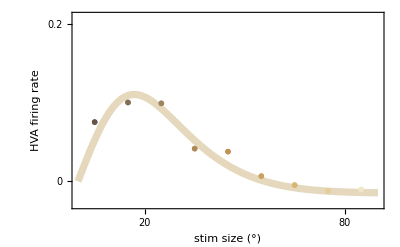

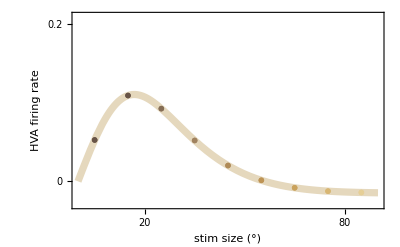

```mathematica
f1=Show[{Plot[Subscript[ri, A][s][[aa]],{s,0,90},Evaluate[optionsf1]],ListPlot[Table[{{sizs[[i]],cents[[i]]}},{i,1,9}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20}]}]
f1f=Show[Plot[Subscript[ri, A][s][[aa]],{s,0,90},Evaluate[optionsf1]],ListPlot[Table[{{sizs[[i]],Subscript[ri, A][sizs[[i]]][[aa]]}},{i,1,9,stepsiz}],PlotStyle->ColorData[colorgrads[[aa]]]/@Join[{0},Range[0,9]/9],PlotMarkers->{●,20}]]
```

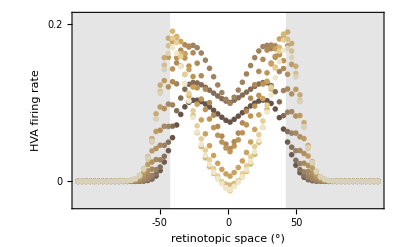

```mathematica
xmin=70;
xmax=360-xmin;
stepsiz=1;
optionsf2list:={PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]stepsiz/9),PlotMarkers->{●,14},DataRange->{-180+xmin,-180+xmax}};
f2=Show[{ListPlot[Table[fieldsub[[sz,xmin;;xmax;;3]],{sz,1,9,stepsiz}],Evaluate[optionsf2],Evaluate[optionsf2list]],Plot[14,{x,-200,-noconfidence[[aa]]},Filling->-1,PlotStyle->Gray],Plot[14,{x,noconfidence[[aa]],200},Filling->-1,PlotStyle->Gray]}]
```

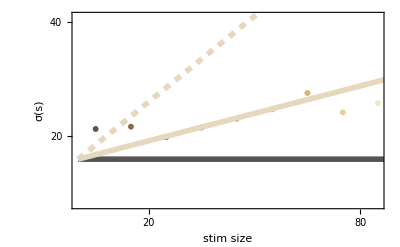

```mathematica
aa=6;
f3=Show[{ListPlot[Table[{{sizs[[sz]],Subscript[σ1dat, A][[aa,sz]]}},{sz,1,9,stepsiz}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},PlotRange->{8,41},Evaluate[optionsf3]],Plot[{σ[s][[aa]],σ[0][[aa]]+s/2,σ[0][[aa]]},{s,0,90},PlotStyle->{{colors[[aa]],Thickness[0.01]},{colors[[aa]],Thickness[0.01],Dashed},{Lighter[Black],Thickness[0.01]}}]}]
```

## Parametrization of input fields (L4,LM&SOM)

```mathematica
optionsf2:={PlotRange->pltrang1[[aa]],Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]stepsiz/9),Method->"DefaultPlotStyle"->Thickness[0.013],FrameLabel->{{Style[StringJoin[who[[aa]]," firing rate"],30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},FrameTicks->{{tickf1[[aa]],None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]]};
```

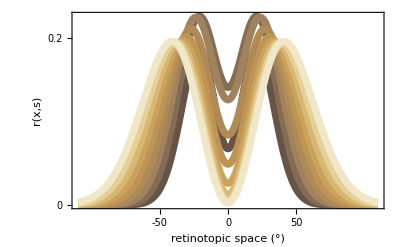

```mathematica
aa=6;
barσFB1[s_]:=(k1+k2 s)^2;
barσFB2[s_]:=(k3+k4 s)^2;
barσRECI1[s_]:=(k5+k6 s)^2;
barσRECI2[s_]:=(k7+k6 s)^2;
barσFF1[s_]:=(k14+k24 s)^2;
barσFF2[s_]:=(k34+k44 s)^2;
r0[s_]:=A1+A2 s;
ρ[s_]=ρ1(Erf[s/sρ1]-Erf[s/sρ2]);
r0S[s_]:=A1S(Erf[s/sA1S]-A2S Erf[s/sA2S]);
ρS[s_]:=ρ1S (Erf[(s-10)/sρ1S]-ρ2S Erf[(s-10)/sρ2S]);
r0FF[s_]:=rff(Erf[s/S1]-ssL4 Erf[s/S2]);
(*parametrizationSOM=Flatten[Import[FileNameJoin[{NotebookDirectory[],"parametersSOM_inverse+.csv"}]]];
parametrizationLM=Flatten[Import[FileNameJoin[{NotebookDirectory[],"parametersLM_inverse+.csv"}]]];
parametrizationL4=Flatten[Import[FileNameJoin[{NotebookDirectory[],"parametersL4_inverse+.csv"}]]];*)
parILM={A1->parametrizationLM[[5]],A2->parametrizationLM[[6]],ρ1->parametrizationLM[[7]],sρ1->parametrizationLM[[8]],sρ2->parametrizationLM[[9]],k1->parametrizationLM[[2]],k2->parametrizationLM[[4]],k3->parametrizationLM[[3]],k4->parametrizationLM[[4]]};
parIL4={rff->parametrizationL4[[5]],ssL4->1,S1->parametrizationL4[[7]],S2->parametrizationL4[[8]],k14-> parametrizationL4[[2]],k24->0,k34-> parametrizationL4[[3]],k44->0};
parISOM={k5->parametrizationSOM[[2]],k7->parametrizationSOM[[3]],k6->parametrizationSOM[[4]],A1S->parametrizationSOM[[5]],A2S->parametrizationSOM[[6]],sA1S->parametrizationSOM[[7]],sA2S->parametrizationSOM[[8]],ρ1S->parametrizationSOM[[9]],ρ2S->parametrizationSOM[[10]],sρ1S->parametrizationSOM[[11]],sρ2S->parametrizationSOM[[12]]};
rFF[x_,y_,s_]:=CFF r0FF[s](Exp[-(x^2+y^2)/(2barσFF1[s])]-Exp[-(x^2+y^2)/(2barσFF2[s])]);
rFB[x_,y_,s_]:=η CFB (r0[s]Exp[-(x^2+y^2)/(2barσFB1[s])]-(r0[s]-ρ[s])Exp[-(x^2+y^2)/(2barσFB2[s])]);
rRECI[x_,y_,s_]:=CRECI (r0S[s]Exp[-(x^2+y^2)/(2barσRECI1[s])]-ρS[s]Exp[-(x^2+y^2)/(2barσRECI2[s])]);
Subscript[pi, A][x_,s_]:={0,0,rRECI[x,0,s],0,rFF[x,0,s],rFB[x,0,s],0};
f2f=Plot[Evaluate@Table[Subscript[pi, A][x,sizs[[sz]]][[aa]]/.parD/.{η->1}/.parISOM/.parIL4/.parILM,{sz,1,9,stepsiz}],{x,-180+xmin,-180+xmax},FrameLabel->{{Style["r(x,s)",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},PlotRange->All,Evaluate[optionsf2]]
```

## Scaling of the maximum of the LM rate field with stimulus size

```mathematica
ttd=Flatten[Table[Ordering[halffield[[s,All]],-1],{s,10,18}]];
sizesd={5,15,25,35,45,55,65,75,85};
```

```mathematica
tt=Table[ArgMax[rFB[x,0,s]/.parILM/.parD/.{η->9},x],{s,1,90,5}];
sizes=Table[s,{s,1,90,5}];
```

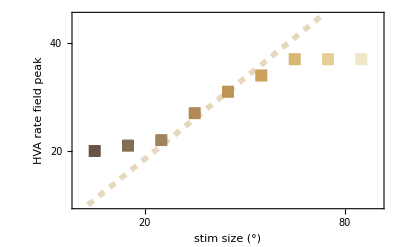

```mathematica
optionsf4:={PlotRange->{10,45},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,
FrameLabel->{{Style[(*"argmax_xr_HVA(x,s)"*)"HVA rate field peak",30,Darker[Gray]],None},{Style["stim size (°)",30,Darker[Gray]],None}},FrameTicks->{{ticksigma[[aa]],None},{{20,80},None}},FrameTicksStyle->Directive[30,Darker[Gray]]};
f4=Show[{Plot[-7.5+σ[0][[aa]]+s/2,{s,0,90},Evaluate[optionsf4],PlotStyle->{{colors[[aa]],Thickness[0.01],Dashed},{colors[[aa]],Thickness[0.01]}}],(*ListPlot[Table[{{sizes[[i]],Abs[tt[[i]]]}},{i,1,Length[tt]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,19]/19),PlotMarkers->{■,8}],*)ListPlot[Table[{{sizesd[[i]],ttd[[i]]-5}},{i,1,9}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->Graphics[{Rectangle[]},ImageSize->12]]}]
```

## Parametrization of HVA

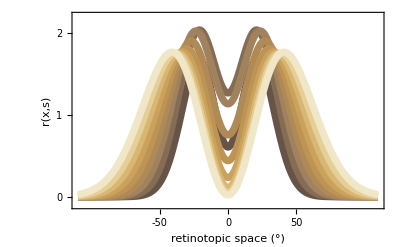

```mathematica
parHVA={η->9};
f2f=Plot[Evaluate@Table[Subscript[pi, A][x,sizs[[sz]]][[aa]]/.parD/.parISOM/.parIL4/.parILM/.parHVA,{sz,1,9,stepsiz}],{x,-180+xmin,-180+xmax},FrameLabel->{{Style["r(x,s)",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},FrameTicks->{{{0,1,2},None},{{-50,0,50},None}},PlotRange->{-.1,2.2},Evaluate[optionsf2]]
```

## Conceptual model L4&LM&SOM inverse

```mathematica
G[x_,y_,σ_]:=Exp[-(x^2+y^2)/(2σ)]/(2π σ);
σFF1[s_]:=σL4+barσFF1[s];(*input from L4 is a ring!*)
σFF2[s_]:=σL4+barσFF2[s];
σFB1[s_]:=σLM+barσFB1[s];
σFB2[s_]:=σLM+barσFB2[s];
σRECI1[s_]:=σSOM+barσRECI1[s];
σRECI2[s_]:=σSOM+barσRECI2[s];
σvi[s_]:=-σr+√(σr (4 σFF1[s]+σr));
σrvi[s_]:=σvi[s]/2+σr;

σmix0[s_]:=σFF1[s] σFF2[s]/(σFF1[s]-σFF2[s]);
σmix1[s_]:=σFF1[s] σFB1[s]/(σFF1[s]-σFB1[s]);
σmix2[s_]:=σFF1[s] σFB2[s]/(σFF1[s]-σFB2[s]);
σmix3[s_]:=σFF1[s] σRECI1[s]/(σFF1[s]-σRECI1[s]);
σmix4[s_]:=σFF1[s]σRECI2[s]/(σFF1[s]-σRECI2[s]);

(*inverse L4 ring sizetuning*)
(*r0FF[s_]:=rff(Erf[s/S1]-ssL4 Erf[s/S2]);*)
rFF[x_,y_,s_]:=CFF r0FF[s](Exp[-(x^2+y^2)/(2barσFF1[s])]-Exp[-(x^2+y^2)/(2barσFF2[s])]);
i0FF1[s_]:=CFF WFF r0FF[s]2π barσFF1[s];
i0FF2[s_]:=-CFF WFF r0FF[s]2π barσFF2[s];

(*inverse LM complex-ring sizetuning*)
(*r0[s_]:=A1+A2 s;
ρ[s_]=ρ1(Erf[s/sρ1]-Erf[s/sρ2]);*)
rFB[x_,y_,s_]=η CFB (r0[s]Exp[-(x^2+y^2)/(2barσFB1[s])]-(r0[s]-ρ[s])Exp[-(x^2+y^2)/(2barσFB2[s])]);
i0FB1[s_]:=η WFB CFB r0[s]2π barσFB1[s];
i0FB2[s_]:=-η WFB CFB(r0[s]-ρ[s])2π barσFB2[s];

(*inverse SOM sizetuning*)
(*r0S[s_]:=A1S(Erf[s/sA1S]-A2S Erf[s/sA2S]);
ρS[s_]:=ρ1S (Erf[(s-10)/sρ1S]-ρ2S Erf[(s-10)/sρ2S]);*)
rRECI[x_,y_,s_]:=CRECI (r0S[s]Exp[-(x^2+y^2)/(2barσRECI1[s])]-ρS[s]Exp[-(x^2+y^2)/(2barσRECI2[s])]);
i0RECI1[s_]:=WRECI r0S[s]2π barσRECI1[s];
i0RECI2[s_]:=-WRECI ρS[s]2π barσRECI2[s];


uI[x_,y_,s_]:= π/w0(σFF1[s]+σrvi[s]) G[x,y,σFF1[s]] (1-√(1-(2 i0FF1[s] w0)/(π (σFF1[s]+σrvi[s]))-(4 σFF1[s]^2 w0)/(σFF1[s]+σrvi[s]) ((i0FF2[s] G[x,y,σmix0[s]])/(σFF1[s]-σFF2[s])+(i0FB1[s] G[x,y,σmix1[s]])/(σFF1[s]-σFB1[s])+(i0FB2[s] G[x,y,σmix2[s]])/(σFF1[s]-σFB2[s])+(i0RECI1[s] G[x,y,σmix3[s]])/(σFF1[s]-σRECI1[s])+(i0RECI2[s] G[x,y,σmix4[s]])/(σFF1[s]-σRECI2[s]))));

frI[x_,y_,s_]=Piecewise[{{uI[x,y,s]^2,uI[x,y,s]>0}},0];
```

## PyrPV with η=1 rather than η=9

```mathematica
frdatai0=Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/sizetuningcurve_Pyr_inv1.csv"}],"Data"]];
profdatai0=Table[Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/spatialprofiles_Pyr_Invsiz",ToString[ssim],"_1.csv"}],"Data"]],{ssim,5,90,10}];
frdatai=Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/sizetuningcurve_Pyr_inv2.csv"}],"Data"]];
profdatai=Table[Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/spatialprofiles_Pyr_Invsiz",ToString[ssim],"_2.csv"}],"Data"]],{ssim,5,90,10}];
ssiz=Table[ssim,{ssim,5,90,10}];
Nn=60;
dx2deg=6;
```

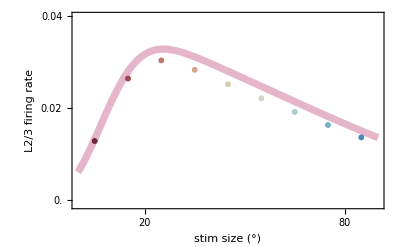

```mathematica
aa=7;
f1=Show[{Plot[frI[0,0,s]/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.{η->1},{s,0,90},PlotRange->{-0.001,0.04},FrameTicks->{{{0.,0.02,0.04},None},{{20,80},None}},Evaluate[optionsf1](*,PlotLegends->Placed[LineLegend[{"analyt"},LabelStyle->{GrayLevel[0.3],26}],{0.37,0.37}]*)],ListPlot[Table[{{ssiz[[s]],frdatai0[[s]]}},{s,1,Length[frdatai0]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20}(*,PlotLegends->Placed[LineLegend[{"simulat"},LabelStyle->{GrayLevel[0.3],26}],{0.37,0.37}]*)]}]
```

## Compare analytics (SOM input=0) with simulations

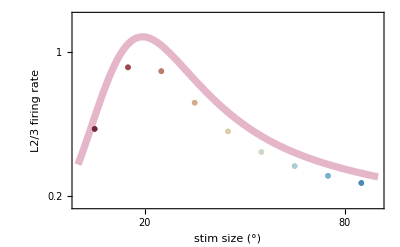

```mathematica
aa=7;
f1=Show[{Plot[frI[0,0,s]/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,{s,0,90},PlotRange->{0.15,1.2},Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"analyt"},LabelStyle->{GrayLevel[0.3],26}],{0.75,0.75}]],
ListPlot[Table[{{ssiz[[s]],frdatai[[s]]}},{s,1,Length[frdatai]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},PlotLegends->Placed[LineLegend[{"simulat"},LabelStyle->{GrayLevel[0.3],26}],{0.75,0.75}]]}]
```

```mathematica
(*SLOW*)
```

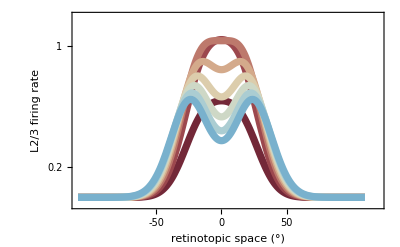

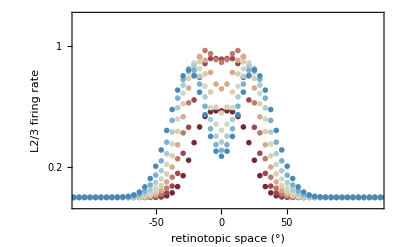

```mathematica
f12=Plot[Evaluate@Table[frI[x,0,s]/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,{s,5,80,10}],{x,-180+xmin,-180+xmax},PlotRange->{{-180+xmin,-180+xmax+10},{-.05,1.2}},Evaluate[optionsf2]]
f22=ListPlot[Table[Table[{-Nn .7dx2deg/2+.7dx2deg x,profdatai[[s,x]]},{x,0,Nn}],{s,1,9}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,14},PlotRange->{{-180+xmin,-180+xmax+10},{-.05,1.2}},Evaluate[optionsf2]]
```

## Analytics SOM input≠0

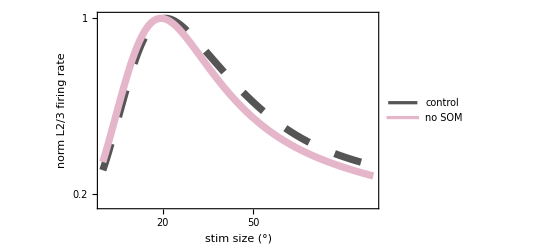

```mathematica
m1=MaxValue[frI[0,0,s]/.parD/.parILM/.parIL4/.parISOM/.parHVA,s];
m2=MaxValue[frI[0,0,s]/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,s];
f4=Plot[{frI[0,0,s]/m1/.parD/.parILM/.parIL4/.parISOM/.parHVA,frI[0,0,s]/m2/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA},{s,0,90},PlotRange->{0.15,1.01},PlotStyle->{{Thickness[0.013],Lighter[Black],Dashing[{0.05,0.05}]},{Thickness[0.013],colors[[7]]}},Evaluate[optionsf1mod]]
```

## Optogenetic Silencing of LM

```mathematica
frdataSili=Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/sizetuningcurve_Pyr_inv3.csv"}],"Data"]];
profdataSili=Table[Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/spatialprofiles_Pyr_Invsiz",ToString[ssim],"_3.csv"}],"Data"]],{ssim,5,90,10}];
ssiz=Table[ssim,{ssim,5,90,10}];
Nn=60;
dx2deg=6;
```

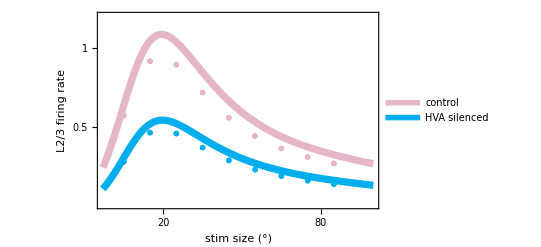

```mathematica
f1=Show[{Plot[{frI[0,0,s]/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,frI[0,0,s]/.parDLMsil/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA},{s,-3,100},PlotRange->{0.01,1.2},PlotStyle->{{colors[[7]],Thickness[0.013]},{RGBColor[0,173/255,237/255],Thickness[0.013]}},FrameTicks->{{{0.5,1},None},{{20,80},None}},Evaluate[optionsf1],
PlotLegends->Placed[LineLegend[{"control","HVA silenced"},LabelStyle->{GrayLevel[0.3],20},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18],{0.7,0.75}]],ListPlot[Table[{{ssiz[[s]],frdatai[[s]]}},{s,1,Length[frdatai]}],PlotStyle->colors[[7]],PlotMarkers->{●,20}],ListPlot[Table[{{ssiz[[s]],frdataSili[[s]]}},{s,1,Length[frdataSili]}],PlotStyle->RGBColor[0,173/255,237/255],PlotMarkers->{●,20}]}]
```

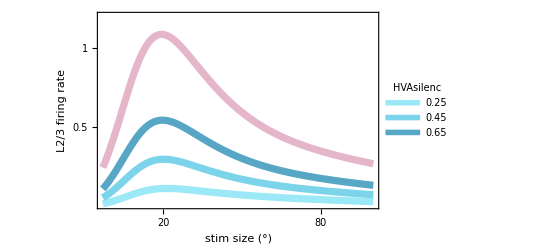

```mathematica
f1=Show[{Plot[Evaluate@Table[frI[0,0,s]/.{CFB->cfb}/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,{cfb,{0.25,0.45,0.65}}],{s,-3,100},PlotRange->{0.01,1.2},PlotStyle->ColorData["BrownCyanTones"]/@(Range[7,9]/9),Method->"DefaultPlotStyle"->Thickness[0.013],FrameTicks->{{{0.5,1},None},{{20,80},None}},Evaluate[optionsf1],
PlotLegends->Placed[LineLegend[Table[ToString[cfb],{cfb,{0.25,0.45,0.65}}],LabelStyle->{GrayLevel[0.3],20},LegendLabel->"HVAsilenc",LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18],{0.78,0.67}]],Plot[frI[0,0,s]/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,{s,-3,100},PlotStyle->{colors[[7]],Thickness[0.013]}]}]
```

## Modifiers on LM

## LM projections too small + Breaking down Convolution

```mathematica
aa=6;
parHVA={η->9};
f2f=Plot[Evaluate@Table[Subscript[pi, A][x,sizs[[sz]]][[aa]]/.parD/.parISOM/.parIL4/.parILM/.parHVA,{sz,1,9,stepsiz}],{x,-180+xmin,-180+xmax},FrameLabel->{{Style["r(x,s)",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},FrameTicks->{{{0,1,2},None},{{-50,0,50},None}},PlotRange->{-.1,2.2},Evaluate[optionsf2]]
```

-Graphics-

```mathematica
optionsf22:={PlotRange->pltrang1[[aa]],Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),Method->"DefaultPlotStyle"->Thickness[0.013],FrameLabel->{{Style["HVA firing rate",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},FrameTicks->{{None,None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]]};
```

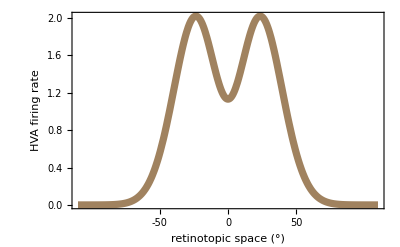

```mathematica
aa=6;
f2f=Plot[Subscript[pi, A][x,sizs[[3]]][[aa]]/.parD/.parISOM/.parIL4/.parILM/.parHVA,{x,-180+xmin,-180+xmax},PlotRange->All,PlotStyle->-Graphics-,Evaluate[optionsf22]]
```

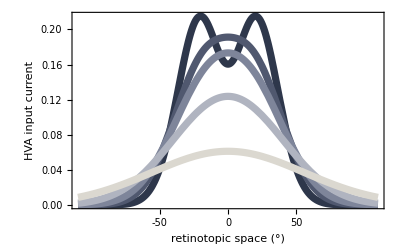

```mathematica
ILM[x_,y_,s_]:=CFB (r0[s]Exp[-(x^2+y^2)/(2barσFB1[s]+2σLM)](2π barσFB1[s])/(2π(barσFB1[s]+σLM))-(r0[s]-ρ[s])Exp[-(x^2+y^2)/(2barσFB2[s]+2σLM)](2π barσFB2[s])/(2π(barσFB2[s]+σLM)));
curr=Plot[Evaluate@Table[ILM[x,0,15]/.σLM->sL^2/.{k4->k2}/.parNOSOM/.parISOM/.parD/.parILM/.parIL4,{sL,{5,15,20,30,50}}],{x,-180+xmin,-180+xmax},FrameLabel->{{Style["HVA input current",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},PlotRange->All,PlotStyle->ColorData["GrayYellowTones"]/@(Range[0,6]/6),Evaluate[optionsf22]]
```

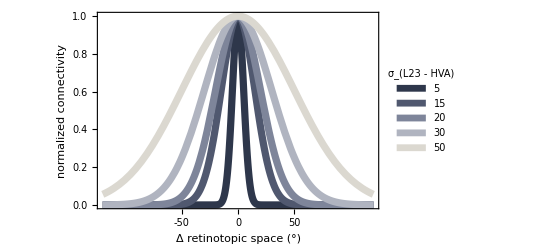

```mathematica
connnect=Plot[Evaluate@Table[2π σLM G[x,0,σLM]/.σLM->sL^2/.{k4->k2}/.parNOSOM/.parISOM/.parD/.parILM/.parIL4,{sL,{5,15,20,30,50}}],{x,-120,120},FrameLabel->{{Style["normalized
connectivity",27,Darker[Gray]],None},{Style["Δ retinotopic space (°)",30,Darker[Gray]],None}},PlotRange->All,PlotStyle->ColorData["GrayYellowTones"]/@(Range[0,6]/6),FrameTicks->{{None,None},{{-50,0,50},None}},Evaluate[optionsf22],PlotLegends->Placed[SwatchLegend[ColorData["GrayYellowTones"]/@(Range[0,6]/6),{"5","15","20","30","50"},LabelStyle->{GrayLevel[0.3],Bold,18},LegendLabel->Placed["σ_(L23 - HVA)",Top],LegendMarkerSize->15],{0.88,0.53}]]
```

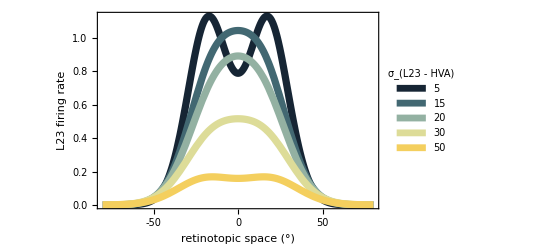

```mathematica
f2=Plot[Evaluate@Table[frI[x,0,15]/.σLM->sL^2/.{k4->k2}/.parNOSOM/.parISOM/.parD/.parILM/.parIL4/.parHVA,{sL,{5,15,20,30,50}}],(*{x,-180+xmin,-180+xmax}*){x,-80,80},FrameLabel->{{Style["L23 firing rate",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},PlotRange->All,PlotStyle->ColorData["StarryNightColors"]/@(Range[0,4]/4),Evaluate[optionsf22],PlotLegends->Placed[SwatchLegend["StarryNightColors",{"5","15","20","30","50"},LabelStyle->{GrayLevel[0.3],Bold,18},LegendLabel->Placed["σ_(L23 - HVA)",Top],LegendMarkerSize->15],{0.88,0.53}]]
```

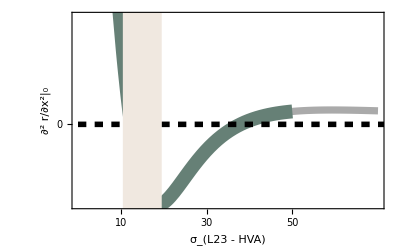

```mathematica
(*SLOW*)
f1=Show[{Plot[D[frI[x,0,15]/.parNOSOM/.σLM->sL^2/.parD/.parILM/.parIL4/.parHVA,{x,2}]/.x->0,{sL,0,70},PlotStyle->{Lighter[Gray],Thickness[0.013]},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["∂^2 r/∂x^2|_0",30,Darker[Gray]],None},{Style["σ_(L23 - HVA)",30,Darker[Gray]],None}},FrameTicks->{{{0},None},{{10,30,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]],GridLines->{{15},None},GridLinesStyle->Directive[LightBrown,Thickness[0.07]]],Plot[D[frI[x,0,15]/.parNOSOM/.σLM->sL^2/.parD/.parILM/.parIL4/.parHVA,{x,2}]/.x->0,{sL,5,50},PlotStyle->Thickness[0.025],ColorFunction->Function[{x,y},ColorData["StarryNightColors"][x]]],Plot[0,{sl,0,80},PlotStyle->{Dashing[{0.015,0.015}],Thickness[0.01],Black}]}]
```

## LM ring not growing + Breaking down Convolution

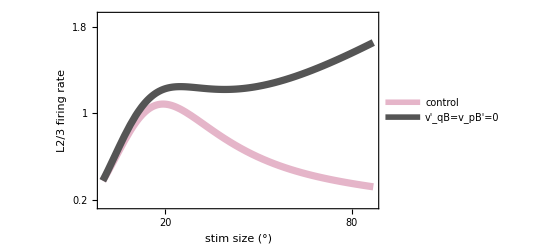

```mathematica
aa=7;
parILMnoks={k2->0,k4->0};
f1=Plot[{frI[0,0,s]/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,frI[0,0,s]/.parILMnoks/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA},{s,0,87},PlotRange->{0.15,1.9},FrameTicks->{{{0.2,1,1.8},None},{{20,80},None}},PlotStyle->{{colors[[aa]],Thickness[0.013]},{Lighter[Black],Thickness[0.013]},{Lighter[Black],Thickness[0.013],Dashing[{0.05,0.05}]},{colors[[2]],Thickness[0.013]}},Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"control","v'_qB=v_pB'=0"},LabelStyle->{GrayLevel[0.3],20},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18],{0.78,0.45}]]
```

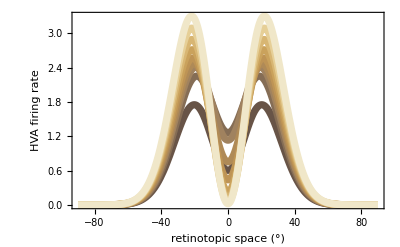

```mathematica
aa=6;
parILMnoks={k2->0,k4->0};
f2f=Plot[Evaluate@Table[Subscript[pi, A][x,sizs[[sz]]][[aa]]/.parD/.parILMnoks/.parISOM/.parIL4/.parILM/.parHVA,{sz,1,9,stepsiz}],{x,-90,90},FrameLabel->{{Style["HVA firing rate",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},PlotRange->All,FrameTicks->{{None,None},{None,None}},Evaluate[optionsf2]]
```

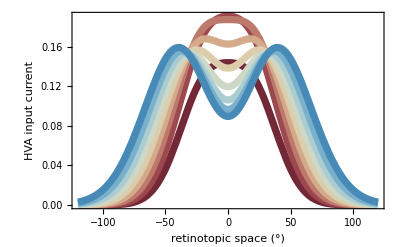

```mathematica
aa=7;
curr=Plot[Evaluate@Table[ILM[x,0,sizs[[sz]]]/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,{sz,1,9,stepsiz}],{x,-120,120},FrameLabel->{{Style["HVA input current",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},PlotRange->All,FrameTicks->{{None,None},{None,None}},Evaluate[optionsf2]]
```

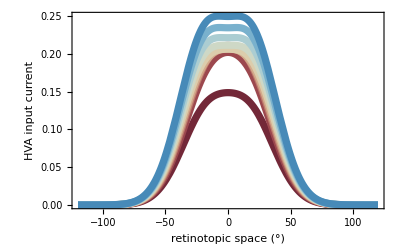

```mathematica
aa=7;
curr=Plot[Evaluate@Table[ILM[x,0,sizs[[sz]]]/.parILMnoks/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,{sz,1,9,stepsiz}],{x,-120,120},FrameLabel->{{Style["HVA input current",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},PlotRange->All,FrameTicks->{{None,None},{None,None}},Evaluate[optionsf2]]
```

## 2D Gaussian centered on a circle

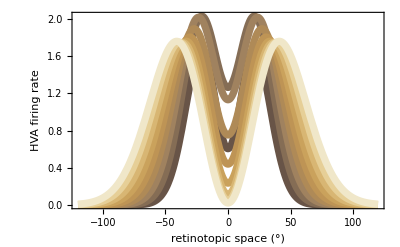

```mathematica
aa=6;
f2f=Plot[Evaluate@Table[Subscript[pi, A][x,sizs[[sz]]][[aa]]/.parD/.parISOM/.parIL4/.parILM/.parHVA,{sz,1,9,stepsiz}],{x,-120,120},FrameLabel->{{Style["HVA firing rate",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},PlotRange->All,FrameTicks->{{None,None},{None,None}},Evaluate[optionsf2]]
```

```mathematica
G2[x_,x0_,v_,A_]:=A( Exp[-((x-x0)^2/(2v))]+Exp[-((x+x0)^2/(2v))])
parHVA2Gaus={{21.4,136,1.655},{21.4,197,2.01},{23.6,221,2.005},{27.3,233.5,1.88},{30.7,226.5,1.8},{33.6,210,1.765},{36.6,200,1.735},{39,182,1.75},{41.3,173.5,1.76}};(*originals*)
```

```mathematica
parHVA2Gaus={{21.4,136,1.655},{21.4,197,2.01},{21.4,221,2.005},{21.4,233.5,1.88},{21.4,226.5,1.8},{21.4,210,1.765},{21.4,200,1.735},{21.4,182,1.75},{21.4,173.5,1.76}};
(*circle radius does not move*)
```

```mathematica
parHVA2Gaus={{21.4,197,2.01},{21.4,197,2.01},{23.6,197,2.01},{27.3,197,2.01},{30.7,197,2.01},{33.6,197,2.01},{36.6,197,2.01},{39,197,2.01},{41.3,197,2.01}};
(*only circle radius moves*)
```

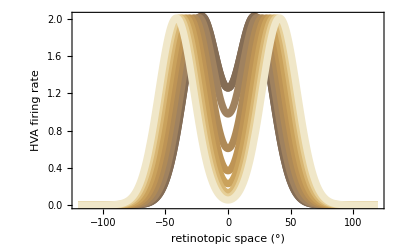

```mathematica
aa=6;
f2f=Plot[Evaluate@Table[G2[x,parHVA2Gaus[[sz,1]],parHVA2Gaus[[sz,2]],parHVA2Gaus[[sz,3]]],{sz,1,9,stepsiz}],{x,-120,120},FrameLabel->{{Style["HVA firing rate",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},PlotRange->All,FrameTicks->{{None,None},{None,None}},Evaluate[optionsf2]]
```

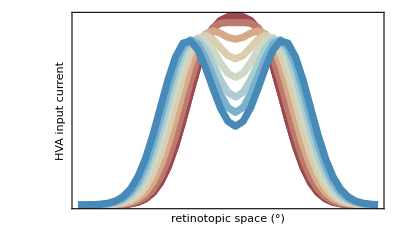

```mathematica
optionsf2in:={PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]),PlotMarkers->{●,14},DataRange->{-100,100}};
aa=7;
fields=Table[Import[StringJoin[{NotebookDirectory[],"1ct/FFInputLM_Invsiz",ToString[sizs[[s]]],"_1991.txt"}],"Data"],{s,1,Length[sizs]}];
f2count=Show[{ListPlot[Table[fields[[sz,30,10;;50]],{sz,1,9}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->None,Joined->True,FrameLabel->{{Style["HVA input current",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},PlotRange->All,FrameTicks->{{None,None},{None,None}},Evaluate[optionsf2],Evaluate[optionsf2in]]}]
```

```mathematica
G2D[x_,y_,r_,v_,A_]:=A Exp[-(Sqrt[x^2+y^2]-r)^2/(2v)]
```

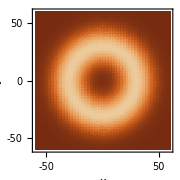

```mathematica
dp=DensityPlot[G2D[x,y,r,v,A]/.{r->30,v->10^2,A->1},{x,-60,60},{y,-60,60},PlotRange->{0,1.3},ImageSize->Small,FrameStyle->Directive[{Darker[Gray],Thickness[0.02]}],FrameLabel->{{Style["y",20,Darker[Gray]],None},{Style["x",20,Darker[Gray]],None}},FrameTicks->{{{-50,0,50},None},{{-50,0,50},None}},LabelStyle->{Darker[Gray],20},ColorFunction->(ColorData["SiennaTones"][Rescale[#,{0,1.3}]]&),ColorFunctionScaling->False,PlotPoints->50,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"σ_(HVA, r)",Ticks->{0,0.5,1}],Below]]
```

```mathematica
frdataiG20=Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/sizetuningcurve_Pyr_inv1989.csv"}],"Data"]];
profdataiG20=Table[Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/spatialprofiles_Pyr_Invsiz",ToString[ssim],"_1989.csv"}],"Data"]],{ssim,5,90,10}];
frdataiG2rconst=Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/sizetuningcurve_Pyr_inv1990.csv"}],"Data"]];
profdataiG2rconst=Table[Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/spatialprofiles_Pyr_Invsiz",ToString[ssim],"_1990.csv"}],"Data"]],{ssim,5,90,10}];
frdataiG2rchange=Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/sizetuningcurve_Pyr_inv1991.csv"}],"Data"]];
profdataiG2rchange=Table[Flatten[Import[StringJoin[{NotebookDirectory[],"1ct/spatialprofiles_Pyr_Invsiz",ToString[ssim],"_1991.csv"}],"Data"]],{ssim,5,90,10}];
ssiz=Table[ssim,{ssim,5,90,10}];
Nn=60;
dx2deg=6;
```

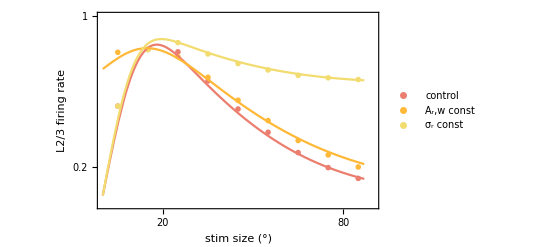

```mathematica
aa=7;
f1=Show[{ListPlot[{Table[{ssiz[[s]],frdataiG20[[s]]},{s,1,Length[frdataiG20]}],Table[{ssiz[[s]],frdataiG2rchange[[s]]},{s,1,Length[frdataiG20]}],Table[{ssiz[[s]],frdataiG2rconst[[s]]},{s,1,Length[frdataiG20]}]},PlotStyle->{ColorData[24]@1,ColorData[24]@2,ColorData[24]@3},PlotMarkers->{●,Small},PlotRange->{{0,90},{0,1}},FrameTicks->{{{0.2,1},None},{{20,80},None}},Evaluate[optionsf1],PlotLegends->Placed[PointLegend[{"control","A_r,w const","σ_r const"},LabelStyle->{GrayLevel[0.3],16}],{0.3,0.32}]],Plot[{0.05+1.25(Erf[s/14]-Erf[s/68]),0.72+(0.47Erf[s/19]-1.1Erf[s/78]),0.05+0.99(Erf[s/12]-0.4Erf[s/60])},{s,0,87},PlotStyle->{ColorData[24]@1,ColorData[24]@2,ColorData[24]@3}]}]
```

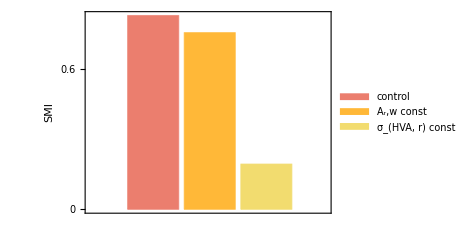

{0.699126,0.82928,0.193732,0.756081}

```mathematica
(*SMI*)
(*measure of SMI*)
(*I am considering the system WITHOUT SOM*)
largesize=85;
SMIctrl=1-(frI[0,0,largesize]/.parNOSOM/.parISOM/.parD/.parILM/.parIL4/.parHVA)/MaxValue[frI[0,0,s]/.parNOSOM/.parISOM/.parD/.parILM/.parIL4/.parHVA,s];
SMIG20=1-(frdataiG20[[9]]/frdataiG20[[2]]);
SMIG2rconst=1-(frdataiG2rconst[[9]]/frdataiG2rconst[[2]]);
SMIG2rchange=1-(frdataiG2rchange[[9]]/frdataiG2rchange[[2]]);
bc=BarChart[{{SMIG20,SMIG2rchange,SMIG2rconst}},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["SMI",27,Darker[Gray]],None},{None,None}},FrameTicks->{{{0,0.6},None},{None,None}},FrameTicksStyle->Directive[30,Darker[Gray]],AspectRatio->1/1.5,ImageSize->350,ChartStyle->24,ChartLegends->{"control","A_r,w const","σ_(HVA, r) const" },LabelStyle->{GrayLevel[0.3],22}]
{SMIctrl,SMIG20,SMIG2rconst,SMIG2rchange}
```

## Contrast

```mathematica
cntrst={0.6,0.7,0.8,0.9,1.};
truecntrst=Log2[2cntrst];
resptolarge=frI[0,0,80]/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA;
SMI=1-Table[(resptolarge/frI[0,0,20]/.{CFF->c,CFB->c})/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,{c,cntrst}];
SMI=SMI/SMI[[Length[SMI]]];
```

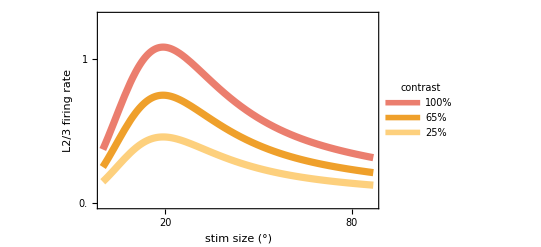

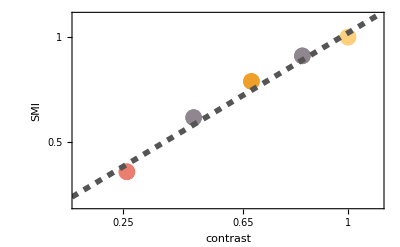

```mathematica
f1=Plot[{frI[0,0,s]/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,frI[0,0,s]/.{CFF->0.8,CFB->0.8}/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA,frI[0,0,s]/.{CFF->0.6,CFB->0.6}/.parNOSOM/.parD/.parILM/.parIL4/.parISOM/.parHVA},{s,0,87},PlotRange->{-0.01,1.3},FrameTicks->{{{0.,1},None},{{20,80},None}},Method->"DefaultPlotStyle"->Thickness[0.013],PlotStyle->ColorData[10]/@{2,3,4},Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"100%","65%","25%"},LabelStyle->{GrayLevel[0.3],20},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18,LegendLabel->"contrast"],{0.8,0.7}]]
f5=Show[{ListPlot[Table[{{truecntrst[[i]],SMI[[i]]}},{i,1,Length[SMI]}],Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["SMI",30,Darker[Gray]],None},{Style["contrast",30,Darker[Gray]],None}},PlotRange->{{0.1,1.1},{.2,1.1}},FrameTicks->{{{.5,1},None},{{.25,.65,1},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotMarkers->{"●",17},PlotStyle->ColorData[10]/@{2,11,3,11,4}],Plot[0.17+0.85c(*1.2-0.85c*),{c,0,1.1},PlotStyle->{Dashed,Lighter[Black],Thickness[0.01]}]}]
```

# SURROUND FACILITATION

## one Gaussian input with orientation ψ, analytics+simulations

```mathematica
ClearAll[Gθ,Gx]
so=FullSimplify[Solve[i0 Gx[x,σ] Gθ[θ-ψ,λ]-a Gx[x,σp] Gθ[θ-ψ,λp]+w0(Gx[x,σEE+σp/2]Gθ[θ-ψ,λEE+λp/2]/(4π Sqrt[σp λp]))a^2==0,a ]];
rules={σp->-σEE+√(4 σ σEE+σEE^2),λp->-λEE+√(4 λ λEE+λEE^2)};
i0:=WL r0 2π Sqrt[ barσ barλ];(*i[x]=i0 G[x,σ=barσ+σL]*)
σ:=barσ+σL;
λ:=barλ+λL;
u[X_,Θ_]:=(a Gx[x,σp] Gθ[θ-ψ,λp])/.so[[1]]/.{θ->Θ,x->X}/.rules;
fr[x_,θ_]:=u[x,θ]^2;
```

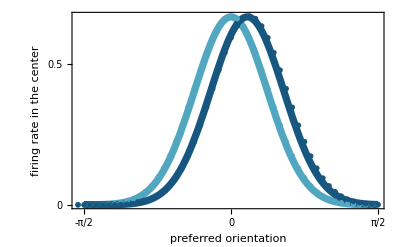

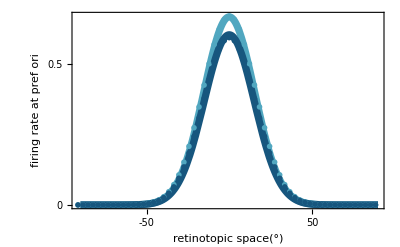

```mathematica
Gθ[θ_,λ_]:=EllipticTheta[3,-θ,ⅇ^(-2 λ)]/π;
Gx[x_,σ_]:=Exp[-x^2/(2σ)]/Sqrt[2π σ];
degtopi=π/180;
par={σEE->8^2,λEE->(degtopi 30)^2,r0->1,w0->-1,WL->1,ψ->0,ψ1->π/2,barσ->20^2,barλ->(10degtopi)^2,σL->8^2,λL->(30degtopi)^2};
parshift=ψ->10degtopi;
(*this has to be made more general!once everything is in the same folder, use relative path (use NotebookDirectory[]).*)
fieldat=Import[StringJoin["/Users/serenadisanto/Dropbox/Allprojects/ColumbiaProjects/Massimo-Andi-Morgane/SSN/HambaradanOri/Ori3D/AllFR_Pyr_Dirsiz20_27.txt"],"Data"];
fieldatshift=Import[StringJoin["/Users/serenadisanto/Dropbox/Allprojects/ColumbiaProjects/Massimo-Andi-Morgane/SSN/HambaradanOri/Ori3D/AllFR_Pyr_Dirsiz20_28.txt"],"Data"];
Nn=Dimensions[fieldat][[1]];
Nt=Dimensions[fieldat][[2]];
dtheta2deg=180/Nt;
fieldthcen=fieldat[[Nn/2+1,All]];
fieldthcenshift=fieldatshift[[Nn/2+1,All]];
f1=Show[Plot[{10fr[0,θ]/.par,10fr[0,θ]/.parshift/.par},{θ,-π/2,π/2},PlotRange->All,PlotRange->All,PlotRange->{{-50,50},{0,0.1}},PlotStyle->(Directive[ColorData[24][#],Thickness[0.013]]&/@{5,7}),Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["firing rate in the center",30,Darker[Gray]],None},{Style["preferred orientation",30,Darker[Gray]],None}},FrameTicks->{{{0,0.5},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[30,Darker[Gray]]],ListPlot[{10fieldthcen,10fieldthcenshift},DataRange->{-π/2-π/Nt,π/2},PlotMarkers->{●,12},PlotStyle->(Directive[ColorData[24][#],Thickness[0.013]]&/@{5,7})]]
dx2deg=3;
fieldx0=fieldat[[All,Nt/2+1]];
fieldx0shift=fieldatshift[[All,Nt/2+1]];
f2=Show[Plot[{10fr[x,0]/.par,10fr[x,0]/.parshift/.par},{x,-dx2deg Nn/2,dx2deg Nn/2},PlotRange->All,PlotRange->{{-50,50},{0,0.1}},PlotStyle->(Directive[ColorData[24][#],Thickness[0.013]]&/@{5,7}),Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["firing rate at pref ori",30,Darker[Gray]],None},{Style["retinotopic space(°)",30,Darker[Gray]],None}},FrameTicks->{{{0,0.5},None},{{-50,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]]],ListPlot[{10fieldx0,10fieldx0shift},DataRange->{-(Nn+1) dx2deg/2,(Nn-1) dx2deg/2},PlotRange->{{-50,50},{0,0.1}},PlotMarkers->{●,12},PlotStyle->(Directive[ColorData[24][#],Thickness[0.013]]&/@{5,7})]]
```

## INVERSE INPUT (one orientation) + DIRECT INPUT (orthogonal orientation) L4+LM+SOM

```mathematica
Quit
2+2
```

```mathematica
(*SLOW*)
(*here i want direct LM ψd + direct SOM ψd + inverse LM ψi + inverse  SOM ψi, i.e. surround with different orientation wrt center + SOM!*)
so=FullSimplify[Solve[iFFi[x,y,θ]+idFF[x,y,θ]+iFBi[x,y,θ]+idFB[x,y,θ]+iSOMi[x,y,θ]+iSOMd[x,y,θ]-a Gx[x,y,σp]((i0dFB+i0SOMd+i0dFF) Gθ[θ-ψd,λp]+(i0iFF1+i0iFF2+i0iFB1+i0iFB2+i0SOMi1+i0SOMi2) Gθ[θ-ψi,λp])+w0 a^2 (Gx[x,y,σEE+σp/2]/(4π σp))((i0dFF+i0dFB+i0SOMd)^2 Gθ[θ-ψd,λEE+λp/2]/(2 Sqrt[π λp])+(i0iFF1+i0iFF2+i0iFB1+i0iFB2+i0SOMi1+i0SOMi2)^2 Gθ[θ-ψi,λEE+λp/2]/(2 Sqrt[π λp])+2(i0dFF+i0dFB+i0SOMd)(i0iFF1+i0iFF2+i0iFB1+i0iFB2+i0SOMi1+i0SOMi2) Gθ[θ-ψd,λEE+λp] Gθ[θ-ψi,λEE+λp])==0,a ]];
rules={σp->-σEE+√(4 σdFB σEE+σEE^2),λp->-λEE+√(4 λ λEE+λEE^2)};
u[X_,Y_,Θ_]:=a Gx[x,y,σp]((i0dFF+i0dFB +i0SOMd)Gθ[θ-ψd,λp]+(i0iFF1+i0iFF2+i0iFB1+i0iFB2+i0SOMi1+i0SOMi2) Gθ[θ-ψi,λp])/.so[[1]]/.{θ->Θ,x->X,y->Y}/.rules;
(*notice that the ansatz is different than before, I include relative weigths of the inputs λ. that's the reason why here i have i0s in all the terms of the equation*)
fr[x_,y_,θ_]:=cλ u[x,y,θ]^2;

λ:=barλ+λL;

(*direct input from LM*)
barσdFB:=(k1+k2 s)^2;
σdFB:=σLM+barσdFB;
r0dFB:=rfb (Erf[s/S3]-ssLM Erf[s/S4]);
i0dFB:=WLM r0dFB 2 π barσdFB Sqrt[2 π barλ];
idFB[x_,y_,θ_]:=i0dFB Gx[x,y,σdFB] Gθ[θ-ψd,λ];

(*direct input from L4*)
σdFF:=σL4+barσdFF;
r0dFF:=rff (Erf[s/S1]-ssL4 Erf[s/S2]);
i0dFF:=WFF r0dFF 2 π barσdFF Sqrt[2 π barλ];
idFF[x_,y_,θ_]:=i0dFF Gx[x,y,σdFF] Gθ[θ-ψd,λ];

(*direct input from SOM*)
barσSOMd:=(k3+k4 s)^2;
σSOMd:=σrecSOM+barσSOMd;
r0SOMd:=rsom(Erf[s/S5]-ssSOM Erf[s/S6]);
i0SOMd:=WESOM r0SOMd 2π barσSOMd Sqrt[2 π  barλ];
iSOMd[x_,y_,θ_]:=i0SOMd Gx[x,y,σSOMd] Gθ[θ-ψd,λ];

(*inverse input from LM*)
barσiFB1:=(ki1+ki2 s)^2;
barσiFB2:=(ki3+ki2 s)^2;
σiFB1:=σLM+barσiFB1;
σiFB2:=σLM+barσiFB2;
r0:=A1+A2 s;
ρ:=ρ1(Erf[s/sρ1]- Erf[s/sρ2]);
i0iFB1:=η WLM r0 2π barσiFB1 Sqrt[ 2 π barλ];
i0iFB2:=-η WLM(r0-ρ)2π barσiFB2 Sqrt[ 2 π barλ];
iFBi[x_,y_,θ_]:=i0iFB1 Gx[x,y,σiFB1] Gθ[θ-ψi,λ]+i0iFB2 Gx[x,y,σiFB2] Gθ[θ-ψi,λ];

(*inverse input from L4*)
barσiFF1:=(k14+k24 s)^2;
barσiFF2:=(k34+k44 s)^2;
σiFF1:=σL4+barσiFF1;(*input from L4 is a ring!*)
σiFF2:=σL4+barσiFF2;
r0FFi:=riff(Erf[s/S1i]-ssiL4 Erf[s/S2i]);
i0iFF1:=WFF r0FFi 2π barσiFF1;
i0iFF2:=-WFF r0FFi 2π barσiFF2;
iFFi[x_,y_,θ_]:=i0iFF1 Gx[x,y,σiFF1] Gθ[θ-ψi,λ]+i0iFF2 Gx[x,y,σiFF2] Gθ[θ-ψi,λ];

(*inverse input from SOM*)
barσSOMi1:=(ki5+ki6 s)^2;
barσSOMi2:=(ki7+ki6 s)^2;
σSOMi1:=σrecSOM+barσSOMi1;
σSOMi2:=σrecSOM+barσSOMi2;
r0S:=A1S(Erf[s/sA1S]-A2S Erf[s/sA2S]);
ρS:=ρ1S (Erf[(s-10)/sρ1S]-ρ2S Erf[(s-10)/sρ2S]);
i0SOMi1:=WESOM r0S 2π barσSOMi1 Sqrt[ 2 π barλ];
i0SOMi2:=-WESOM ρS 2π barσSOMi2 Sqrt[2 π  barλ];
iSOMi[x_,y_,θ_]:=i0SOMi1 Gx[x,y,σSOMi1] Gθ[θ-ψi,λ]+i0SOMi2 Gx[x,y,σSOMi2] Gθ[θ-ψi,λ];
```

```mathematica
nbd=NotebookDirectory[];
(*load from files parameters from datasets, direct stim*)
Subscript[σ, AB]={{7,5,4,0,7,15},{5,6,6,0,5,15},{8,6,0,6,0,15},{5,6,6,0,0,15}};
parErffitd=Import[FileNameJoin[{nbd,"parameters_sizetunings_direct+.csv"}]];
tabd=parErffitd[[;;,4;;7]];
bd=Join[parErffitd[[;;,1]],{0}];
kdc=parErffitd[[;;,2]];(*THESE ARE IN DEGREES*)
kd=parErffitd[[;;,3]];
parametrizationSOM=Flatten[Import[FileNameJoin[{nbd,"parametersSOM_inverse+.csv"}]]];
parametrizationLM=Flatten[Import[FileNameJoin[{nbd,"parametersLM_inverse+.csv"}]]];
parametrizationL4=Flatten[Import[FileNameJoin[{nbd,"parametersL4_inverse+.csv"}]]];

parD={σEE->(Subscript[σ, AB][[1,1]])^2,σL4->(Subscript[σ, AB][[1,5]])^2,σLM->(Subscript[σ, AB][[1,6]])^2,σrecSOM->(Subscript[σ, AB][[1,3]])^2,w0->-.1,WESOM->-0.15,WLM->.75,WFF->1.};
parDLM={rfb->tabd[[6,1]],k1->kdc[[6]],k2->kd[[6]],ssLM->tabd[[6,2]]/tabd[[6,1]],S3->tabd[[6,3]],S4->tabd[[6,4]]};
parDSOM={rsom->tabd[[3,1]],ssSOM->tabd[[3,2]]/tabd[[3,1]],k3->kdc[[3]],k4->kd[[3]],S5->tabd[[3,3]],S6->tabd[[3,4]]};
parNOSOM=WESOM->-0.;
parNOLM=WLM->0.4;
parDL4={rff->tabd[[5,1]],ssL4->tabd[[5,2]]/tabd[[5,1]],S1->tabd[[5,3]],S2->tabd[[5,4]],barσdFF->kdc[[5]]^2};
parILM={A1->parametrizationLM[[5]],A2->parametrizationLM[[6]],ρ1->parametrizationLM[[7]],sρ1->parametrizationLM[[8]],sρ2->parametrizationLM[[9]],ki1->parametrizationLM[[2]],ki2->parametrizationLM[[4]],ki3->parametrizationLM[[3]],ki4->parametrizationLM[[4]],η->8};
parISOM={ki5->parametrizationSOM[[2]],ki7->parametrizationSOM[[3]],ki6->parametrizationSOM[[4]],A1S->parametrizationSOM[[5]],A2S->parametrizationSOM[[6]],sA1S->parametrizationSOM[[7]],sA2S->parametrizationSOM[[8]],ρ1S->parametrizationSOM[[9]],ρ2S->parametrizationSOM[[10]],sρ1S->parametrizationSOM[[11]],sρ2S->parametrizationSOM[[12]]};
parIL4={riff->parametrizationL4[[5]],ssiL4->1,S1i->parametrizationL4[[7]],S2i->parametrizationL4[[8]],k14-> parametrizationL4[[2]],k24->0,k34-> parametrizationL4[[3]],k44->0};
parλ={λEE->(degtopi 30)^2,barλ->(degtopi 15)^2,λL->(degtopi 30)^2,ψd->0,ψi->degtopi 90,s->15,cλ->10};
parcent={A1->0,A2->0,ρ1->0,A1S->0,ρ1S->0,riff->0};
pariso=s->50;
parinv={rfb->0,rsom->0,rff->0};
Gθ[θ_,λ_]:=EllipticTheta[3,-θ,ⅇ^(-2 λ)]/π;
Gx[x_,y_,σ_]:=Exp[-(x^2+y^2)/(2σ)]/(2π σ);
degtopi=π/180;
```

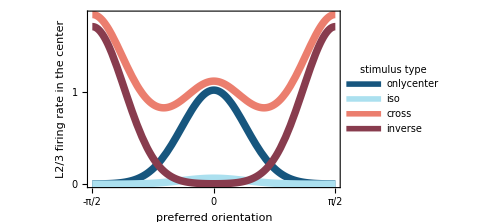

```mathematica
(*SLOW*)
frcent[x_,θ_]:=fr[x,0,θ]/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
friso[x_,θ_]:=fr[x,0,θ]/.parcent/.pariso/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frcross[x_,θ_]:=fr[x,0,θ]/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frinv[x_,θ_]:=fr[x,0,θ]/.parinv/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
f1=Plot[{frcent[0,θ],friso[0,θ],frcross[0,θ],frinv[0,θ]},{θ,-90degtopi,90degtopi},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["L2/3 firing rate
in the center",27,Darker[Gray]],None},{Style["preferred orientation",27,Darker[Gray]],None}},FrameTicks->{{{0,1},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotLegends->LineLegend[{"onlycenter","iso","cross","inverse"},LabelStyle->{GrayLevel[0.3],24},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.2,LegendLabel->"stimulus type"],PlotStyle->ColorData[24]/@{7,4,1,9},ImageSize->Medium]
```

## Comparison L4+LM+SOM vs noLM vs noSOM

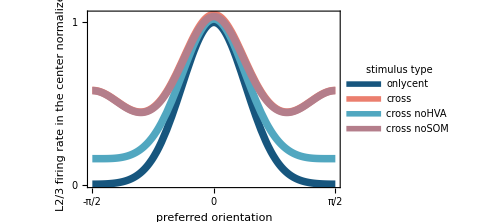

```mathematica
(*VERY SLOW*)
(*frcent[x_,θ_]:=fr[x,0,θ]/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frcross[x_,θ_]:=fr[x,0,θ]/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frcrossnoSOM[x_,θ_]:=fr[x,0,θ]/.parNOSOM/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frcennoSOM[x_,θ_]:=fr[x,0,θ]/.parNOSOM/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frcrossnoLM[x_,θ_]:=fr[x,0,θ]/.parNOLM/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frcennoLM[x_,θ_]:=fr[x,0,θ]/.parNOLM/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
n1=frcent[0,0];
n2=frcennoSOM[0,0];
n3=frcennoLM[0,0];
f1=Plot[{frcent[0,θ]/n1,frcross[0,θ]/n1,frcrossnoLM[0,θ]/n3,frcrossnoSOM[0,θ]/n2},{θ,-90degtopi,90degtopi},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["L2/3 firing rate
in the center
normalized",25,Darker[Gray]],None},{Style["preferred orientation",25,Darker[Gray]],None}},FrameTicks->{{{0,1},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotLegends->LineLegend[{"onlycent","cross","cross noHVA","cross noSOM"},LabelStyle->{GrayLevel[0.3],24},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.2,LegendLabel->"stimulus type"],PlotStyle->ColorData[24]/@{7,1,5,8},ImageSize->Medium]*)
```

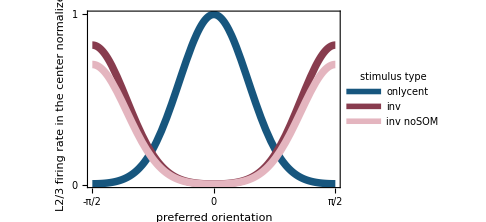

```mathematica
(*frcent[x_,θ_]:=fr[x,0,θ]/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frinv[x_,θ_]:=fr[x,0,θ]/.parinv/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frinvnoSOM[x_,θ_]:=fr[x,0,θ]/.parinv/.parNOSOM/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frcennoSOM[x_,θ_]:=fr[x,0,θ]/.parNOSOM/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
n1=frcent[0,0];
n2=frcennoSOM[0,0];
f1=Plot[{frcent[0,θ]/n1,frinv[0,θ]/n1,frinvnoSOM[0,θ]/n2},{θ,-90degtopi,90degtopi},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["L2/3 firing rate
in the center
normalized",25,Darker[Gray]],None},{Style["preferred orientation",25,Darker[Gray]],None}},FrameTicks->{{{0,1},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotLegends->LineLegend[{"onlycent","inv","inv noSOM"},LabelStyle->{GrayLevel[0.3],24},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.2,LegendLabel->"stimulus type"],PlotStyle->ColorData[24]/@{7,9,10},ImageSize->Medium]*)
```

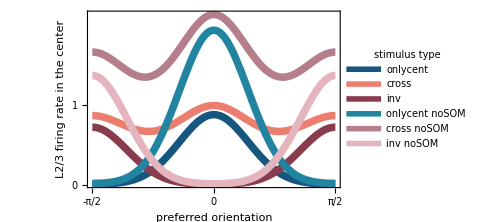

```mathematica
(*frcent[x_,θ_]:=fr[x,0,θ]/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frcross[x_,θ_]:=fr[x,0,θ]/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frinv[x_,θ_]:=fr[x,0,θ]/.parinv/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frcrossnoSOM[x_,θ_]:=fr[x,0,θ]/.parNOSOM/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frcennoSOM[x_,θ_]:=fr[x,0,θ]/.parNOSOM/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frinvnoSOM[x_,θ_]:=fr[x,0,θ]/.parinv/.parNOSOM/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
f1=Plot[{frcent[0,θ],frcross[0,θ],frinv[0,θ],frcennoSOM[0,θ],frcrossnoSOM[0,θ],frinvnoSOM[0,θ]},{θ,-90degtopi,90degtopi},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["L2/3 firing rate
in the center",27,Darker[Gray]],None},{Style["preferred orientation",27,Darker[Gray]],None}},FrameTicks->{{{0,1},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotLegends->LineLegend[{"onlycent","cross","inv","onlycent noSOM","cross noSOM","inv noSOM"},LabelStyle->{GrayLevel[0.3],24},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.2,LegendLabel->"stimulus type"],PlotStyle->ColorData[24]/@{7,1,9,6,8,10},ImageSize->Medium]*)
```

```mathematica
parλ={λEE->(degtopi 33)^2,barλ->(degtopi 15)^2,λL->(degtopi 33)^2,ψd->0,ψi->degtopi 90,s->15,cλ->10};
```

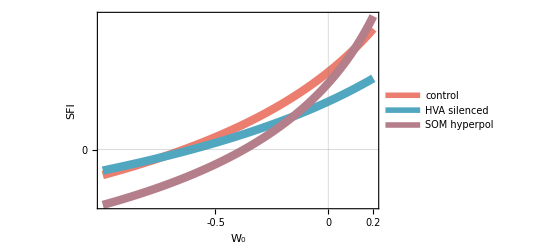

```mathematica
frw0crns[W_]:=fr[0,0,0]/.{w0->W}/.parNOSOM/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frw0cens[W_]:=fr[0,0,0]/.{w0->W}/.parNOSOM/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frw0cr[W_]:=fr[0,0,0]/.{w0->W}/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frw0ce[W_]:=fr[0,0,0]/.{w0->W}/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frw0crnl[W_]:=fr[0,0,0]/.{w0->W}/.parNOLM/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
frw0cenl[W_]:=fr[0,0,0]/.{w0->W}/.parNOLM/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
f3=Plot[{(frw0cr[W0]-frw0ce[W0])/(frw0cr[W0]+frw0ce[W0]),(frw0crnl[W0]-frw0cenl[W0])/(frw0crnl[W0]+frw0cenl[W0]),(frw0crns[W0]-frw0cens[W0])/(frw0crns[W0]+frw0cens[W0])},{W0,-1,0.2},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["SFI",30,Darker[Gray]],None},{Style["W_0",30,Darker[Gray]],None}},FrameTicks->{{{0,0.5},None},{{-0.5,0,0.2},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotStyle->ColorData[24]/@{1,5,8},GridLines->{{0},{0}},PlotLegends->LineLegend[{"control","HVA silenced","SOM hyperpol"},LabelStyle->{GrayLevel[0.3],24}]]
```

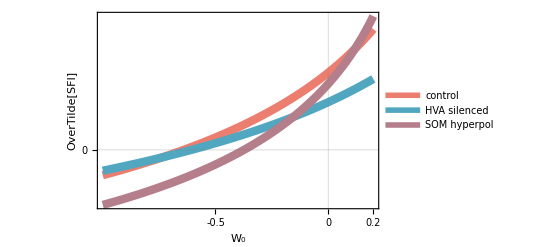

```mathematica
uw0crns[W_]:=u[0,0,0]/.{w0->W}/.parNOSOM/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
uw0cens[W_]:=u[0,0,0]/.{w0->W}/.parNOSOM/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
uw0cr[W_]:=u[0,0,0]/.{w0->W}/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
uw0ce[W_]:=u[0,0,0]/.{w0->W}/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
uw0crnl[W_]:=u[0,0,0]/.{w0->W}/.parNOLM/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
uw0cenl[W_]:=u[0,0,0]/.{w0->W}/.parNOLM/.parcent/.parD/.parDL4/.parDLM/.parDSOM/.parIL4/.parILM/.parISOM/.parλ;
f3=Plot[{(uw0cr[W0]-uw0ce[W0])/(uw0cr[W0]+uw0ce[W0]),(uw0crnl[W0]-uw0cenl[W0])/(uw0crnl[W0]+uw0cenl[W0]),(uw0crns[W0]-uw0cens[W0])/(uw0crns[W0]+uw0cens[W0])},{W0,-1,0.2},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style[OverTilde["SFI"],30,Darker[Gray]],None},{Style["W_0",30,Darker[Gray]],None}},FrameTicks->{{{0,0.5},None},{{-0.5,0,0.2},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotStyle->ColorData[24]/@{1,5,8},GridLines->{{0},{0}},PlotLegends->LineLegend[{"control","HVA silenced","SOM hyperpol"},LabelStyle->{GrayLevel[0.3],24}]]
```

## Breakdown of the inputs

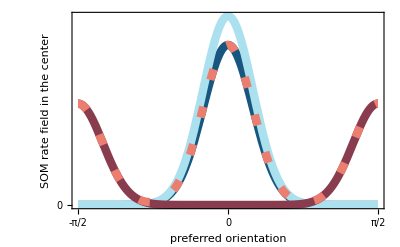

```mathematica
rSOMi[x_,θ_]:=(r0S 2π barσSOMi1 Gx[x,0,σSOMi1]-ρS 2π barσSOMi2 Gx[x,0,σSOMi2])Gθ[θ-ψi,barλ]Sqrt[2π barλ];
rSOMd[x_,θ_]:= r0SOMd Exp[-x^2/(2barσSOMd)] Gθ[θ-ψd,barλ]Sqrt[2π barλ];
fSOM=Plot[{rSOMd[0,θ]/.parD/.parDSOM/.parλ,rSOMd[0,θ]/.pariso/.parD/.parDSOM/.parλ,rSOMi[0,θ]/.parD/.parISOM/.parλ,(rSOMd[0,θ]+rSOMi[0,θ])/.parD/.parDSOM/.parISOM/.parλ},{θ,-π/2,π/2},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,(*PlotLabel->Style["LM input current",30,Darker[Gray]],*)Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["SOM rate field
 in the center",27,Darker[Gray]],None},{Style["preferred orientation",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[30,Darker[Gray]],(*PlotLegends->LineLegend[{"onlycenter","cross","inverse"},LabelStyle->{GrayLevel[0.3],Bold,22}],*)PlotStyle->{{ColorData[24]@7},{ColorData[24]@4},{ColorData[24]@9},{ColorData[24]@1,Dashing[{0.02,0.05}]}}]
```

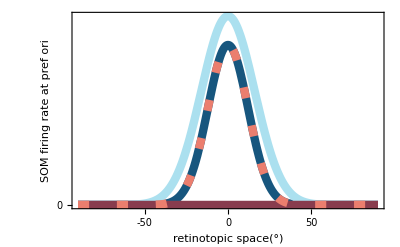

```mathematica
fSOM=Plot[{rSOMd[x,0]/.parD/.parDSOM/.parλ,rSOMd[x,0]/.pariso/.parD/.parDSOM/.parλ,rSOMi[x,0]/.parD/.parISOM/.parλ,(rSOMd[x,0]+rSOMi[x,0])/.parD/.parDSOM/.parISOM/.parλ},{x,-90,90},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["SOM firing rate 
at pref ori",27,Darker[Gray]],None},{Style["retinotopic space(°)",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotStyle->{{ColorData[24]@7},{ColorData[24]@4},{ColorData[24]@9},{ColorData[24]@1,Dashing[{0.02,0.05}]}}]
```

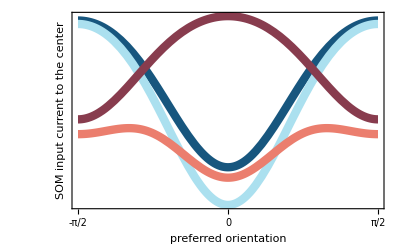

```mathematica
fSOM=Plot[{iSOMd[0,0,θ]/.parD/.parDSOM/.parλ,iSOMd[0,0,θ]/.pariso/.parD/.parDSOM/.parλ,iSOMi[0,0,θ]/.parD/.parISOM/.parλ,(iSOMd[0,0,θ]+iSOMi[0,0,θ])/.parD/.parDSOM/.parISOM/.parλ},{θ,-π/2,π/2},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,(*PlotLabel->Style["LM input current",30,Darker[Gray]],*)Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["SOM input current
to the center",27,Darker[Gray]],None},{Style["preferred orientation",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[30,Darker[Gray]],(*PlotLegends->LineLegend[{"onlycenter","cross","inverse"},LabelStyle->{GrayLevel[0.3],Bold,22}],*)PlotStyle->ColorData[24]/@{7,4,9,1}]
```

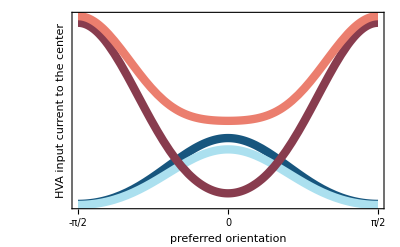

```mathematica
fLM=Plot[{idFB[0,0,θ]/.parD/.parDLM/.parλ,idFB[0,0,θ]/.pariso/.parD/.parDLM/.parλ,iFBi[0,0,θ]/.parD/.parILM/.parλ,(idFB[0,0,θ]+iFBi[0,0,θ])/.parD/.parDLM/.parILM/.parλ},{θ,-π/2,π/2},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,(*PlotLabel->Style["LM input current",30,Darker[Gray]],*)Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["HVA input current
to the center",27,Darker[Gray]],None},{Style["preferred orientation",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[30,Darker[Gray]],(*PlotLegends->LineLegend[{"onlycenter","cross","inverse"},LabelStyle->{GrayLevel[0.3],Bold,22}],*)PlotStyle->ColorData[24]/@{7,4,9,1}]
```

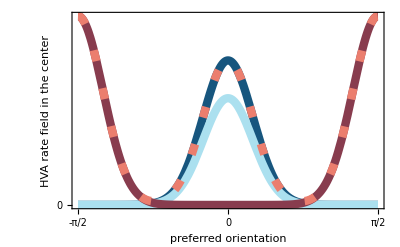

```mathematica
rFBi[x_,θ_]:=η(r0 2π barσiFB1 Gx[x,0,barσiFB1]-(r0-ρ)2π barσiFB2 Gx[x,0,barσiFB2])Gθ[θ-ψi,barλ]Sqrt[2π barλ];
rFBd[x_,θ_]:= r0dFB 2π barσdFB Gx[x,0,barσdFB] Gθ[θ-ψd,barλ]Sqrt[2π barλ];
prfLM=Plot[{rFBd[0,θ]/.parD/.parDLM/.parλ,rFBd[0,θ]/.pariso/.parD/.parDLM/.parλ,rFBi[0,θ]/.parD/.parILM/.parλ,(rFBd[0,θ]+rFBi[0,θ])/.parD/.parDLM/.parILM/.parλ},{θ,-π/2,π/2},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["HVA rate field
in the center",27,Darker[Gray]],None},{Style["preferred orientation",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotStyle->{{ColorData[24]@7},{ColorData[24]@4},{ColorData[24]@9},{ColorData[24]@1,Dashing[{0.02,0.05}]}}]
```

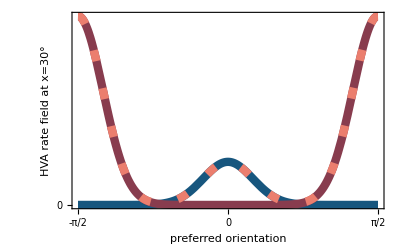

```mathematica
prfLM=Plot[{rFBd[30,θ]/.parD/.parDLM/.parλ,(*rFBd[30,θ]/.pariso/.parD/.parDLM/.parλ,*)rFBi[30,θ]/.parD/.parILM/.parλ,(rFBd[30,θ]+rFBi[30,θ])/.parD/.parDLM/.parILM/.parλ},{θ,-π/2,π/2},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["HVA rate field
at x=30°",27,Darker[Gray]],None},{Style["preferred orientation",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotStyle->{{ColorData[24]@7}(*,{ColorData[24]@4}*),{ColorData[24]@9},{ColorData[24]@1,Dashing[{0.02,0.05}]}}]
```

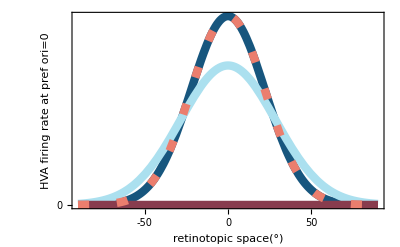

```mathematica
fLM=Plot[{rFBd[x,0]/.parD/.parDLM/.parλ,rFBd[x,0]/.pariso/.parD/.parDLM/.parλ,rFBi[x,0]/.parD/.parILM/.parλ,(rFBd[x,0]+rFBi[x,0])/.parD/.parDLM/.parILM/.parλ},{x,-90,90},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["HVA firing rate 
at pref ori=0",27,Darker[Gray]],None},{Style["retinotopic space(°)",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotStyle->{{ColorData[24]@7},{ColorData[24]@4},{ColorData[24]@9},{ColorData[24]@1,Dashing[{0.02,0.05}]}}]
```

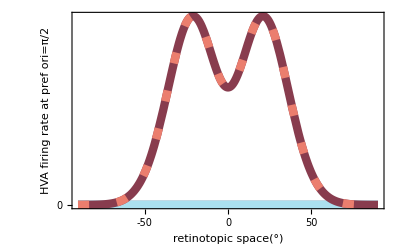

```mathematica
fLM=Plot[{rFBd[x,π/2]/.parD/.parDLM/.parλ,rFBd[x,π/2]/.pariso/.parD/.parDLM/.parλ,rFBi[x,π/2]/.parD/.parILM/.parλ,(rFBd[x,π/2]+rFBi[x,π/2])/.parD/.parDLM/.parILM/.parλ},{x,-90,90},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["HVA firing rate 
at pref ori=π/2",27,Darker[Gray]],None},{Style["retinotopic space(°)",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotStyle->{{ColorData[24]@7},{ColorData[24]@4},{ColorData[24]@9},{ColorData[24]@1,Dashing[{0.02,0.05}]}}]
```

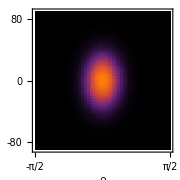
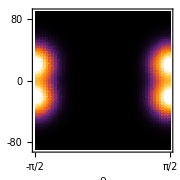
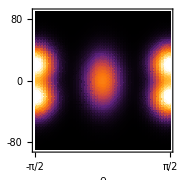

```mathematica
clarification2=Row[{DensityPlot[rFBd[x,θ]/.parD/.parDLM/.parλ,{θ,-π/2,π/2},{x,-90,90},PlotRange->{0,1.6},ImageSize->Small,FrameStyle->Directive[{ColorData[24]@7,Thickness[0.045]}],FrameLabel->{{Style["x",26,ColorData[24]@7],None},{Style["θ",26,ColorData[24]@7],None}},FrameTicks->{{{-80,0,80},None},{{-π/2,0,π/2},None}},LabelStyle->{ColorData[24]@7,26},ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1.6}]]&),ColorFunctionScaling->False,PlotPoints->50],DensityPlot[rFBi[x,θ]/.parD/.parILM/.parλ,{θ,-π/2,π/2},{x,-90,90},PlotRange->{0,1.6},ImageSize->Small,FrameStyle->Directive[{ColorData[24]@9,Thickness[0.045]}],FrameLabel->{{Style["x",26,ColorData[24]@9],None},{Style["θ",26,ColorData[24]@9],None}},FrameTicks->{{{-80,0,80},None},{{-π/2,0,π/2},None}},LabelStyle->{ColorData[24]@9,26},ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1.6}]]&),ColorFunctionScaling->False,PlotPoints->50],DensityPlot[(rFBd[x,θ]+rFBi[x,θ])/.parD/.parDLM/.parILM/.parλ,{θ,-π/2,π/2},{x,-90,90},PlotRange->{0,1.6},ImageSize->Small,FrameStyle->Directive[{ColorData[24]@1,Thickness[0.045]}],FrameLabel->{{Style["x",26,ColorData[24]@1],None},{Style["θ",26,ColorData[24]@1],None}},FrameTicks->{{{-80,0,80},None},{{-π/2,0,π/2},None}},LabelStyle->{ColorData[24]@1,26},ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1.6}]]&),ColorFunctionScaling->False,PlotPoints->50]}]
```

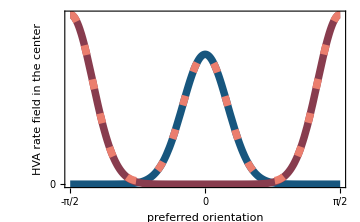
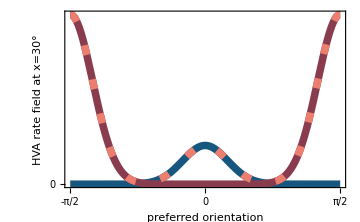

```mathematica
clarificationtheta=Row[{Plot[{rFBd[0,θ]/.parD/.parDLM/.parλ,(*rFBd[0,θ]/.pariso/.parD/.parDLM/.parλ,*)rFBi[0,θ]/.parD/.parILM/.parλ,(rFBd[0,θ]+rFBi[0,θ])/.parD/.parDLM/.parILM/.parλ},{θ,-π/2,π/2},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["HVA rate field
in the center",27,Darker[Gray]],None},{Style["preferred orientation",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[27,Darker[Gray]],PlotStyle->{{ColorData[24]@7},(*{ColorData[24]@4},*){ColorData[24]@9},{ColorData[24]@1,Dashing[{0.02,0.05}]}},ImageSize->Medium],Plot[{rFBd[30,θ]/.parD/.parDLM/.parλ,(*rFBd[30,θ]/.pariso/.parD/.parDLM/.parλ,*)rFBi[30,θ]/.parD/.parILM/.parλ,(rFBd[30,θ]+rFBi[30,θ])/.parD/.parDLM/.parILM/.parλ},{θ,-π/2,π/2},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["HVA rate field
at x=30°",27,Darker[Gray]],None},{Style["preferred orientation",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-π/2,0,π/2},None}},FrameTicksStyle->Directive[27,Darker[Gray]],PlotStyle->{{ColorData[24]@7}(*,{ColorData[24]@4}*),{ColorData[24]@9},{ColorData[24]@1,Dashing[{0.02,0.05}]}},ImageSize->Medium]}]
```

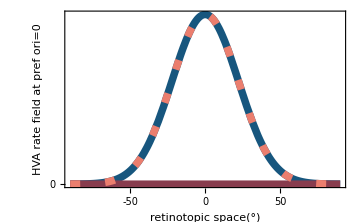
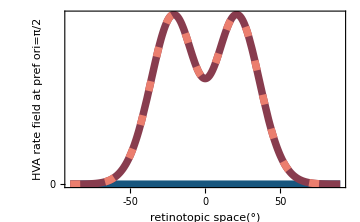

```mathematica
clarificationx=Row[{Plot[{rFBd[x,0]/.parD/.parDLM/.parλ,(*rFBd[x,0]/.pariso/.parD/.parDLM/.parλ,*)rFBi[x,0]/.parD/.parILM/.parλ,(rFBd[x,0]+rFBi[x,0])/.parD/.parDLM/.parILM/.parλ},{x,-90,90},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["HVA rate field 
at pref ori=0",27,Darker[Gray]],None},{Style["retinotopic space(°)",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotStyle->{{ColorData[24]@7},(*{ColorData[24]@4},*){ColorData[24]@9},{ColorData[24]@1,Dashing[{0.02,0.05}]}},ImageSize->Medium],Plot[{rFBd[x,π/2]/.parD/.parDLM/.parλ,(*rFBd[x,π/2]/.pariso/.parD/.parDLM/.parλ,*)rFBi[x,π/2]/.parD/.parILM/.parλ,(rFBd[x,π/2]+rFBi[x,π/2])/.parD/.parDLM/.parILM/.parλ},{x,-90,90},PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,Method->"DefaultPlotStyle"->Thickness[0.015],FrameLabel->{{Style["HVA rate field 
at pref ori=π/2",27,Darker[Gray]],None},{Style["retinotopic space(°)",27,Darker[Gray]],None}},FrameTicks->{{{0},None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]],PlotStyle->{{ColorData[24]@7},(*{ColorData[24]@4},*){ColorData[24]@9},{ColorData[24]@1,Dashing[{0.02,0.05}]}},ImageSize->Medium]}]
```